5

多值函数  解析延拓   Γ函数

复变函数与实变函数的重要区别之一就是涉及多值函数这一概念。

回顾在复变函数定义中的表述：

对于复变量在某一个区域取的每一个复数值 z=x+ⅈ y，

按照一定的规律，有一个或多个复数值 w=u+ⅈ v 与之相对应。

因此，可以是多个复数值与一个自变量值相对应，这就是多值函数。

最简单的多值函数例子是根式函数，如平方根。

人们不能像实变函数的平方根那样规定只取算术根作为平方根函数。理由很简单：

对实变函数，当实自变量沿实轴离开某点之后又返回该点时，平方根的函数值必然返回到原来的值。

对复变函数，平方根的函数值是否回原来的值，与自变量离开再返回起点的路径有关

（参见下一节的详细分析）。因此不能规定只取单一个函数值。

多值函数不仅带来复杂性，还带来一定的混乱。最简单的例子是伯努利诡论：

(-z)^2=z^2  ⟹   (Ln(-z))^2=Ln z^2   ⟹   Ln(-z)+Ln(-z)=Ln z+Ln z

⟹   2Ln(-z)=2Ln z   ⟹   Ln(-z)=Ln z   ⟹   ⅇ^(Ln(-z))=ⅇ^(Ln z)   ⟹   -z=z

现在知道，该诡论的错误之处在于没有考虑到函数的多值性。

实际上：Ln z+Ln z ≠2 Ln z，因为 Ln z 是多值函数，函数值对应于一个集合（而不是单一个数），因而

Ln z+Ln z 为两个集合的并（和集），当然不会等于一个集合中的每一个元素都乘于 2。

然而，前面介绍的复变函数的导数、解析等概念，都是基于单值函数而言。

那么，对于多值函数，如何推广？

## 5.1 多值函数及其Riemann面

实际上，对多值函数，在能唯一确定其函数值之前，难以引入导数、解析等概念。

因此，对多值函数，需要先确定函数值。而确定了函数值之后，则可以应用单值函数的概念与性质。

确定多值函数的函数值，需要三个步骤：枝点，割线，上下岸。下称为三要素。

枝点：绕其一周回到出发点时，函数 w=f(z) 的值发生改变，称之为函数 f(z)的枝点。

函数之所以会出现多值，是因为在复平面上，当自变量离开某点，

在复平面上经一条闭合路径，回到原出发点时，函数值可能发生改变。例如：

w=√z⟹^定义 √(|z|)ⅇ^(ⅈ θ/2),   其中 θ 为 z 的辐角，即：θ=arg z

如图，从 A 点出发，沿绿色闭合线走一周回 A 点
z 的辐角 θ 不变，因而函数值 w 回到原来的数值
同样出发于 A 点，沿白色线走一周返到 A 点，
辐角 θ 增加了 2π，（行走过程辐角 θ 始终增加）
函数值 w ⟹ -w，不回到原来的数值
即：沿某些闭路回起始点，函数值会发生改变，
          而对另外一些闭路径，函数值不变。
为此，引进枝点概念区分不同的路径。    -Graphics-

上例中， z=0 是函数 w=√z 的枝点，因为绕 z=0 行走一周后回到出发点，函数值发生改变。

如何找出多值函数的枝点：

基于定义：在枝点邻域绕行一周回到出发点，函数值发生改变。

利用（实变函数的）求导法则对函数求导，导函数的奇点通常（很可能）是原函数的枝点，

当然要再对这些候选点利用枝点的定义进行判断。

w=√z,  w'=1/(2 √z),  z=0为 w' 的奇点，故它可能是 w 的枝点，再利用枝点的定义判断。

与判断奇点和求留数类似，判断枝点时，别忘了绕无穷远一周判断无穷远点是否枝点。

一个多值函数，枝点通常多于一个。

枝点阶数：若绕一周改变函数值，绕两周返回原函数值，则称为一阶枝点，

绕 n 周回原函数值，则称为 n-1 阶枝点。

枝点是奇点，因为枝点 z_0 是不同单值分支的公共点， z 从不同单值分支趋于 z_0，

因不同单值分支的函数值 f(z) 不同，导致极限值 lim _(z→z_0) (f(z)-f(z_0))/(z-z_0)不同

也即：极限与 z 趋于 z_0 的方式有关，导数不存在 —— 奇点

更简单的理解是：直接趋于 z_0 和绕 z_0 折腾几周再趋于 z_0 ，接近 z_0 时 f(z)不同，极限值不同，导数不存在。

割线：连接（所有）枝点的直线或曲线

所做的割线应满足：每一个枝点都有割线连出，并且割线只能起始、终止于枝点。（类似于电荷和电场线）

做完割线之后，在复平面内，任何路径都不可能不穿过割线而绕枝点一周。

因此，若规定任何路径均不可穿过割线，就不存在绕枝点的路径，因而函数值就能唯一确定了。

也可这样理解，当路径到达割线并继续延续时，就进入函数的另一个单值分支，

进入另一个复平面，这些复平面通过割线相粘接，构成多叶Riemann面。

w=√z =√(|z|)ⅇ^(ⅈ θ/2)  的 Riemann 面，是个二叶 Riemann 面     （颜色表征辐角大小，从 0 到 4π）

-Graphics3D-      -Graphics3D-

如上图，从正实轴出发，辐角为 0，绕原点逆时针转一周，辐角增为 2π，

若继续逆时针转，辐角自然继续增加，对平方根函数 w=√(|z|)ⅇ^(ⅈ  (arg z)/2)，

辐角 arg z 增加 2π，函数值会发生变化，因此可视为进入下一叶Riemann 面，

若继续逆时针转 2π，辐角比原出发点增加了 4π，函数值回原来的初始值，

因此可视为返回原来的那叶Riemann 面，这就构成了上图的二叶 Riemann 面。

做了割线，就防止了从一叶Riemann 面，跑到另一叶Riemann 面，

只能在同一叶Riemann 面上，自然就保持单值了。

作完割线后，函数尽管是单值的（在复平面内任意行走，只要不穿过割线，回到出发点时，函数值还原），

但是尚不能确定是取多值集合中的哪一个函数值，或者说，还没有确定是在哪一叶 Riemann 面上

因此还需要下一步。

上下岸辐角：定义割线上岸或下岸的辐角，或者给定函数在某点的函数值。

对多值函数，割线上（下）岸的辐角定义可以不同，相应的，函数值也不同。

这称为选取多值函数的不同单值分支。或称为选取 Riemann 面的不同叶

例如方根函数 w=√z =√(|z|)ⅇ^(ⅈ θ/2)  如上图的二叶 Riemann 面，

可取辐角在 [0,2π] 的一叶，也可取辐角在 [2π,4π] 的一叶

无论选取哪一叶，只要不穿过割线，函数就是单值的。

除了上述三要素之外，还有一种方法可确定函数值：

即：给定某一点的函数值以及从该点出发到达复平面任意一点的路径。

因为沿着确定的路径走，辐角的增量是确定的，函数值也就确定了。

即使做好割线并定义上下岸辐角值，枝点是奇点。枝点甚至不是孤立奇点。

如何理解：在 z 趋于枝点 z_0 时，可直接趋于 z_0，也可绕着 z_0 转一圈再趋于 z_0

导致极限值 lim _(z→z_0) (f(z)-f(z_0))/(z-z_0)不同 ，故导数不存在。

不可导特性不会因为做了割线之后就成为可导

或者说：在枝点，即使一阶导数存在，也不能保证任意阶导数一定存在，如：z^(3/2)

故枝点是非解析点。

做割线只是为了方便讨论多值函数众多单值分支中的某个特定单值分支，

或者是为了方便逐一讨论各个单值分支的特性。

而不是简单粗暴地将多值函数指定成在某个特定单值分支上的单值函数。

也就是，对于本来丰富多彩的多值函数，我们不是简单地选取一个，舍去其余，

而是通过枝点、割线、上下岸等三要素，把所有可能的单值分支都罗列出来，

然后逐一研究在各个单值分支（单值函数）。

以下通过例题说明枝点、割线、上下岸等概念。

例题：讨论多值函数 w=f(z)=√(z^2-1)。

解：据函数的定义：w=√(z^2-1)=√(|z-1||z+1|)ⅇ^(ⅈ (θ_1+θ_2)/2),   θ_1=arg(z-1),  θ_2=arg(z+1)

θ_1=arg(z-1)  等于从 1到 z 的矢量与实轴正向的夹角；

θ_2=arg(z+1)  =arg[z-(-1)]  为从-1到 z 的矢量与实轴正向的夹角；

-Graphics-        -Graphics-

要确定函数值，需要三要素：枝点、割线、上下岸。

w=√(z^2-1)=√(|z-1||z+1|)ⅇ^(ⅈ (θ_1+θ_2)/2),    θ_1=arg(z-1),   θ_2=arg(z+1)

枝点：试着求导：w'=(2z)/(√(z^2-1))的奇点 z=±1可能是枝点，同时别忘了判断 z=∞ 是否枝点

在 z=1邻域绕 z=1逆时针一周回出发点，θ_1 增加了 2π，θ_2 不变，w  ⟹ -w, 是枝点；

在 z=-1邻域绕 z=-1逆时针一周回出发点，θ_1 不变，θ_2 增加了 2π，w  ⟹ -w, 也是枝点；

在 z=∞ 邻域绕 z=∞ 逆时针一周回出发点，θ_1 增加了 2π，θ_2 也增加了 2π，w 不变，不是枝点。

故：函数 w=√(z^2-1) 有两个枝点 z=±1。

割线：连接枝点（保证每一个枝点都有割线连出），为简单起见，取直线。

可以选直接连接 z=±1的直线，如左图紫色线段，

也可以为从 z=1，经无穷远点再到达 z=-1的直线，如右图蓝色的直 线

上（下）岸：指定辐角值

如左图，割线取为连接 z=±1的直线，
  (θ^)_1=arg_^(z-1),   θ_2=arg(z+1)
w_=√(z^2-1)=√(|z-1||z+1|)ⅇ^(ⅈ (θ_1+θ_2)/2)
上岸：{θ_1=π，3π
θ_2=_ 0^,  2π， 组合成 4 种情况，
但 (θ_1+θ_2)/2=π/2,(3π)/2,(5π)/2
                              只给出两种不同的函数值
设上岸辐角取为：{θ_1=π
θ_2=0，     -Graphics-

下举例说明如何确定复平面辐角 θ_1 与 θ_2，确定了辐角，函数值就确定

当 z=ⅈ 时，{θ_1=π-π/4，从上岸的点到达 z=ⅈ，矢量 (z-1)顺时针转了 π/4
θ_2=0+π/4,  从上岸的点到达 z=ⅈ，矢量 (z+1)逆时针转了 π/4

z=-ⅈ 时，{θ_1=π+π/4，从上岸沿蓝色路径到 z=-ⅈ，(z-1)逆时针转了 π/4
θ_2=0+(7π)/4,  从上岸沿蓝色路径到 z=-ⅈ，(z+1)逆时针转了(7π)/4

z=-ⅈ 时，{θ_1=π-(7π)/4，从上岸沿红色路径到 z=-ⅈ，(z-1)顺时针转了(7π)/4
θ_2=0-π/4,  从上岸沿红色路径到 z=-ⅈ，(z+1)顺时针转了 π/4

故：w(z)=√(|z^2-1|)ⅇ^(ⅈ (θ_1+θ_2)/2)   ⟹   {w(ⅈ)=√2 ⅇ^(ⅈ/2 (π-π/4+0+π/4))=√2 ⅈ
w(-ⅈ)=√2 ⅇ^(ⅈ/2(π+π/4+(7π)/4))=-√2ⅈ   从上岸沿蓝色路径到 z=-ⅈ   
 w(-ⅈ)=√2 ⅇ^(ⅈ/2(-(3π)/4-π/4))=-√2ⅈ    从上岸沿红色路径到 z=-ⅈ

计算辐角时应注意：

a)  需从已知辐角值的点出发，经一条不穿过割线的路径到达所需要求函数值的点

b)  计算 θ_1 和 θ_2 时必须沿同一条路径，即：计算 θ_1 和 θ_2 都用上图的蓝色路径，

或都用红色路径，不可以用红色路径计算 θ_1，却用蓝色路径计算 θ_2。

可以验证，上岸辐角取为：{θ_1=3π
θ_2=2π  函数值相同，与{θ_1=π
θ_2=0属同一个单值分支。

设上岸辐角取为：{θ_1=π
θ_2=2π，可以求出 z=ⅈ 时的 θ_1 与 θ_2

故：{w(ⅈ)=√2 ⅇ^(ⅈ/2 (π-π/4+2π+π/4))=-√2ⅈ
w(-ⅈ)=√2 ⅇ^(ⅈ/2(π+π/4+2π+(7π)/4))=√2 ⅈ         ⟹     w(ⅈ)=-w(-ⅈ)

可以验证，上岸辐角取为：{θ_1=3π
θ_2=0  函数值相同，与{θ_1=π
θ_2=2π属同一个单值分支。

故函数 w=√(z^2-1) 有两个单值分支。至于属哪一个单值分支，可以由上岸辐角值确定。

也可以由复平面上任意一点的函数值确定。

例如作完割线后给定 w(ⅈ)=-√2ⅈ, 就确定了单值分支，w(-ⅈ)=?

-Graphics-

设沿上图蓝色线从 z=ⅈ  到 z=-ⅈ，依旧：θ_1=arg(z-1), θ_2=arg(z+1)

w(ⅈ)=√(|ⅈ-1||ⅈ+1|)ⅇ^(ⅈ/2(θ_1+θ_2))=√2 ⅇ^(ⅈ/2(θ_1+θ_2))=-√2ⅈ

⟹   在 z=ⅈ 处：  ⅇ^(ⅈ/2(θ_1+θ_2))=-ⅈ

沿蓝色线到 z=-ⅈ，{θ_1 ⟶ θ'_1= θ_1+π/2       矢量 z-1 逆时针转了 π/2
θ_2 ⟶ θ'_2=θ_2+(3π)/2    矢量 z+1逆时针转了 (3π)/2

w(-ⅈ)=√(|-ⅈ-1||ⅈ+1|)ⅇ^(ⅈ/2(θ'_1+θ'_2))=√2 ⅇ^(ⅈ/2 (θ_1+θ_2+2π))=√2 ⅈ

沿红色线到 z=-ⅈ，{θ_1 ⟶ θ'_1= θ_1-(3π)/2
θ_2 ⟶ θ'_2=θ_2-π/2，

w(-ⅈ)=√(|-ⅈ-1||ⅈ+1|)ⅇ^(ⅈ/2(θ'_1+θ'_2))=√2 ⅇ^(ⅈ/2 (θ_1+θ_2-2π))=√2 ⅈ

-Graphics-

若取上图割线，并定义 w(ⅈ)=-√2ⅈ，则：w(-ⅈ)=-√2ⅈ=w(ⅈ)

若取上岸：{θ_1=0
θ_2=0，则：w(ⅈ)=√2 ⅈ=w(-ⅈ)

若取上岸：{θ_1=2π
θ_2=0，则：w(ⅈ)=-√2ⅈ=w(-ⅈ)

可见，取不同的割线，函数的“奇偶性”不同。

取直接连接 z=±1的直线作为割线，w(-ⅈ)=-w(ⅈ)，“奇函数”

若取连接 z=1，∞，-1的直线作为割线，w(-ⅈ)=w(ⅈ)，“偶函数”

在做割线之前，不能判断 w=√(z^2-1)是否满足：w(-z_0)=w(z_0)，这点与实函数不同。

例题：为函数 w=f(z)=√(z^2-1) 做割线，使得当 z 在实轴上时，w 退化为：w=g(x)=Piecewise[{{√(x^2-1),, |x|≥1}, {ⅈ √(1-x^2),, |x|<1}}]。

解：需要做什么样的割线，并如何定义辐角值，才能保证 f(z)在实轴上退化为 g(x)?

-Graphics-        -Graphics-

从前题知：z=±1是 f(z)=√(z^2-1) 的枝点，可以有两种不同的割线

左图的割线必导致 w(-2)=-w(2)，显然不能退化为   g(x)，下证之。

设在 z=2时，arg(z-1)=θ_1,    arg(z+1)=θ_2,  w(2)=√(|2^2-1|)ⅇ^(ⅈ(θ_1+θ_2)/2)=√3 ⅇ^(ⅈ(θ_1+θ_2)/2)

沿左图白色路径到达 z=-2

在 z=-2时，arg(z-1)=θ'_1=θ_1+π,     arg(z+1)=θ'_2=θ_2+π,

w(-2)=√(|2^2-1|)ⅇ^(ⅈ(θ'_1+θ'_2)/2)=√3 ⅇ^(ⅈ(θ_1+π+θ_2+π)/2)=-√3 ⅇ^(ⅈ(θ_1+θ_2)/2)=-w(2)

因此，取左图割线无法使得当 z 在实轴上时，f(z)退化为 g(x)，无论在哪一个单值分支。

只能取如右图之割线。在右割线的上岸，定义  arg(z-1)=θ_1=0, arg(z+1)=θ_2=0

对实轴上 x≥1，取右割线上岸的函数值，w(z)=√(|x^2-1|)ⅇ^(ⅈ(θ_1+θ_2)/2)=√(x^2-1)

对实轴上  x≤-1，取左割线下岸的函数值，θ'_1=θ_1+π,  θ'_2=θ_2-π

θ'_1+θ'_2=θ_1+θ_2=0,  仍有：w(z)=√((|x|)^2-1)ⅇ^(ⅈ( θ'_1+θ'_2)/2)=√(x^2-1)

对实轴上  |x|<1，有：θ''_1=θ_1+π, θ''_2= θ_2,

θ''_1+θ''_2=θ_1+π+θ_2=π,  故：w(z)=√(|x^2-1|)ⅇ^(ⅈ/2(θ''_1+θ''_2))=√(1-x^2)ⅇ^(ⅈ π/2)=ⅈ √(1-x^2)

例题：已知函数 w=f(z)=√(z^2-1) 在实轴上退化为：w(x)=Piecewise[{{√(x^2-1),, |x|≥1}, {ⅈ √(1-x^2),, |x|<1}}]，

求：w'(2) 、 w'(2+ⅈ) 和 w'(2-ⅈ)

-Graphics-

解：取如上图蓝色之割线。定义：θ_1≡arg(z-1),    θ_2≡arg(z+1)

在右上岸，取 θ_1=θ_2=0，在实轴上即可退化为所要求的函数（见上一题）。

因为三要素（枝点、割线、上岸辐角值）均已定，故 w=√(z^2-1)实际上已经是单值函数。

当然，枝点 z=±1 是函数的奇点，除枝点与无穷远点 z=∞ 外，函数在复平面内解析。

w'(z)=f'(z)   ⟹^求导法则同实变函数  w'(z)=z/(√(z^2-1))

在实轴 z=2，必须取右割线上岸的点，才能满足题意，

故：在 z=2，θ_1=0,  θ_2=0

((w'(2)=2/(√3 ⅇ^(ⅈ/2(θ_1+θ_2)))=2/(√3),    与实函数比较： w'(x)|)_(x=2)=x/(√(x^2-1))|)_(x=2)=2/(√3)

(w'(2+ⅈ)=z/(√(z^2-1))|)_(z=2+ⅈ)=(2+ⅈ)/(√(|2+ⅈ+1||2+ⅈ-1|)ⅇ^(ⅈ/2(θ_1+θ_2)))=(2+ⅈ)/20^(1/4)ⅇ^(-ⅈ/2(π/4+arctg 1/3))

其中：从右割线上岸到 z=2+ⅈ，θ_1=π/4，θ_2=arctg 1/3

(w'(2-ⅈ)=z/(√(z^2-1))|)_(z=2-ⅈ)=(2-ⅈ)/(√(|2-ⅈ+1||2-ⅈ-1|)ⅇ^(ⅈ/2(θ_1+θ_2)))=(2-ⅈ)/20^(1/4)ⅇ^(-ⅈ/2((7π)/4-arctg 1/3))

其中：从右割线上岸到 z=2-ⅈ，θ_1=(7π)/4，θ_2=-arctg 1/3（顺时针）

例题：设 w(z)=√(z(1-z)) ，试根据下述条件计算：w(-1) 。

作割线连接 z=0 和 z=1，并规定在割线上岸：θ_1≡arg(z)=0，θ_2≡arg(1-z)=0；

不作割线，规定 arg w(1/2)=0， z 分别沿如右图路径 C_1与 C_2 从 1/2 移动到 z=-1。

-Graphics-       -Graphics-       割线为从 z=0到 z=1的线段，
右图路径 C_2 与 C_4 相当于穿过割线，
函数值与经 路径 C_1 与 C_3
到达 z=-1时的函数值不同。

解：i. 在割线上岸，θ_1=θ_2=0

如沿 L_1 从上岸到达 z=-1， θ_1=arg(z)=0+π,  θ_2=arg(1-z)=0+0

⟹ w(-1)=√2 ⅇ^(ⅈ/2(θ_1+θ_2))=√2 ⅈ

如果沿 L_2 从上岸到达 z=-1， θ_1=0-π,  θ_2=0-2π

⟹ w(-1)=√2 ⅇ^(ⅈ/2(θ_1+θ_2))=√2 ⅇ^(ⅈ/2(-3π))=√2 ⅈ

结果是相等的，在做好割线之后，只要路径不穿过割线，函数值就唯一确定。

当然，必须沿相同的路径求两个辐角 θ_1 与 θ_2 （同为红或同为绿色路径）

ii. 不做割线，规定在 z=1/2, arg w(1/2)=0,   记得： θ_1=arg(z),  θ_2=arg(1-z)

即 z=1/2 时，θ_1=θ_1^0, θ_2=θ_2^0,  arg w(1/2)=(θ_1^0+θ_2^0)/2  ⟹  (θ_1^0+θ_2^0)=0,

沿 红色路径 C_1 到达 z=-1时，θ_1=θ_1^0+π, θ_2=θ_2^0, ⟹ w(-1)=√2 ⅇ^(ⅈ/2(θ_1^0+π+θ_2^0))=√2 ⅈ

沿蓝色路径  C_2 到达 z=-1时，θ_1=θ_1^0+3π, θ_2=θ_2^0, ⟹ w(-1)=√2 ⅇ^(ⅈ/2(θ_1^0+3π+θ_2^0))=-√2ⅈ

可见，沿 C_2, 相当于穿过左图的割线（橙色线），必跑到另一个单值分支，函数值发生改变。

思考：若取割线为连接 z=0，∞，1的直线，沿 C_2 路径会跑到另一个单值分支吗？

若沿绿色路径  C_3 到达 z=-1，θ_1=θ_1^0+π, θ_2=θ_2^0, ⟹ w(-1)=√2 ⅇ^(ⅈ/2(θ_1^0+π+θ_2^0))=√2 ⅈ

沿 C_3 未穿过割线，仍在同一个单值分支，函数值仍为 √2 ⅈ。

思考：若取割线为连接 z=0，∞，1的直线，沿 C_3 路径会跑到另一个单值分支吗？

若沿紫色路径  C_4 到达 z=-1，θ_1=θ_1^0-π, θ_2=θ_2^0, ⟹ w(-1)=√2 ⅇ^(ⅈ/2(θ_1^0-π+θ_2^0))=-√2ⅈ

▲    这里为了与左图比较，选取 z=1/2  时   (θ_1^0+θ_2^0)=0，

已隐含了 z=1/2 点相当于在左图割线的上岸，

这样左图沿 L_1 与右图沿 C_1 到达 z=-1点函数值一致。

从而沿紫色路径  C_4 相当于穿过割线（ 右图橙色线）

跑到另一个单值分支，函数值不再等于 √2 ⅈ。

例题：函数 w(z)=√(z-ⅇ^(ⅈ ϕ)) ,  (0<ϕ<π/2)，在 z=0 的值 w(0)=ⅇ^(ⅈ/2(ϕ+π))，z 从 z_0=0 出发沿直线到达 z_1=ⅇ^(-ⅈ ϕ), 求 w(z_1)

解：属“给定某点的函数值及到达新点的路径，求新点的函数值”问题。

据函数的定义：w(z)=√(|z-ⅇ^(ⅈ ϕ)|)ⅇ^(ⅈ θ/2),  其中： θ≡arg (z-ⅇ^(ⅈ ϕ))

θ 为从 ⅇ^(ⅈ ϕ) 到 z 这个矢量与正实轴方向的夹角

z=0时，w(0)=ⅇ^(ⅈ θ/2)=ⅇ^(ⅈ(ϕ+π)/2), 故：z=0时，θ_0=π+ϕ

z 从 z_0=0 出发沿直线 l 到达 z_1=ⅇ^(-ⅈ ϕ)，

θ_1=θ_0+((π-2ϕ)/2)^(⏞^(角 ∠OBA))=(3π)/2， 角OBA 就是从 z_0=0到 z_1=ⅇ^(-ⅈ ϕ)上图红色箭头扫过的角度

故：w(ⅇ^(-ⅈ ϕ))=√(|ⅇ^(-ⅈ ϕ)-ⅇ^(ⅈ ϕ)|)ⅇ^(ⅈ θ_1/2)=√(2sin ϕ)ⅇ^(ⅈ 3π/4)

例题：函数 w(z)=ln(1-z^2)，已知 w(0)=0, 求 w(3)与 w(3ⅈ)。

注：对数函数 ln ζ 的定义为
       ln ζ=ln|ζ|+ⅈ  arg ζ
可以验证： 
     ζ=0 与 ζ=∞ 是无穷阶枝点，
绕枝点行走，函数永远不回原值
函数 ln z 的 Riemann 面如右图
（z 轴和颜色标记辐角大小）
逆时针绕原点 arg ζ 恒增，
函数值 ln ζ=ln|ζ|+ⅈ  arg ζ 总在变 -Graphics3D-

解：由对数函数的定义：w(z)=ln|1-z^2|+ⅈ [arg(1-z)+arg(z+1)],

枝点：z=±1 和 ∞，做割线如左图，连接三个枝点。

-Graphics-

也可做割线如右图。

现做如右图割线：w(z)=ln|1-z^2|+ⅈ [arg(1-z)+arg(z+1)],

令：θ_1≡arg(1-z),   θ_2=arg(z+1)

z=z_0=0时：w(0)=ⅈ(θ_1^0+θ_2^0)=0, ⟹   θ_1^0+θ_2^0=0

z=z_1=3时：沿 C_1 从 z_0 到 z_1，θ_1=θ_1^0+π, θ_2=θ_2^0, w(3)=ln 8+ⅈ π

z=z_2=3ⅈ 时：沿 C_2 从 z_0 到 z_2，θ_1=θ_1^0+(2π-arctg 3), θ_2=θ_2^0+arctg 3, w(3ⅈ)=ln 10+2ⅈ π

思考：若做如左图割线，会有什么不同？

例题：求积分：I_1=∫_0^∞ cos x^p ⅆx ,  I_2=∫_0^∞ sin x^p ⅆx      (p>1)    超越普利瓦洛夫留数卷 p89

解：取 f(z)=ⅇ^(ⅈ z^p), 积分回路包含大圆弧，应用大圆弧引理

大圆弧作到什么角度？    lim_(z→∞) z f(z)  有界的方位

lim_(z→∞) z f(z)=lim_(z→∞) z ⅇ^(ⅈ z^p),    大圆弧：z=R ⅇ^(ⅈ θ)
=lim_(R→∞) R ⅇ^(ⅈ θ)ⅇ^(ⅈ R^p cos p θ-R^p sin p θ)
 仅当  sin p θ>0 时，
才满足大圆弧引理条件：lim_(z→∞) z f(z)=存在   -Graphics-

0<θ<π/p 时，有   ∫_C_R f(z)ⅆz=0

设大圆弧为 π/(2p)圆弧，

回路为：正实轴 L_1，π/(2p)圆弧 C_R， L_2：z=r ⅇ^(ⅈ π/2p)，C_r  小圆弧

为何要做小圆弧：因为 z=0 是枝点，枝点是奇点，奇点如官员出行：“威武”，“回避”

多值函数：枝点 z=0, ∞，

割线：从 0 沿正实轴到无穷远 C_1，或从 0 沿负实轴到无穷远 C_2

辐角：若割线取为 C_1，定义其上岸 z 的辐角为 0，在上岸 f(z)=ⅇ^(ⅈ x^p)

若割线取为 C_2，定义正实轴 z 的辐角为 0，在正实轴 f(z)=ⅇ^(ⅈ x^p)

C_R： ∫_C_R f(z)ⅆz=0， 
C_r： ∫_C_r f(z)ⅆz  ⟹^小圆弧引理  lim_(r→0) ∫_C_r f(z)ⅆz=0
L_1：∫_L_1 f(z)ⅆz=∫_0^∞ ⅇ^(ⅈ x^p)ⅆx,      -Graphics-

若割线取为 C_1，L_1 必须取在上岸，记得：f(z)=ⅇ^(ⅈ z^p)

L_2：  z=r ⅇ^(ⅈ π/2p),     z^p=ⅈ r^p,          一旦确定了 L_1 的辐角，L_2 的辐角也就确定了

∫_L_2 f(z)ⅆz=-∫_0^∞ ⅇ^(ⅈ (ⅈ r^p))ⅇ^(ⅈ π/2p)ⅆr=-ⅇ^(ⅈ π/2p)∫_0^∞ ⅇ^(-r^p)ⅆr=-1/pΓ(1/p)ⅇ^(ⅈ π/2p)

其中：∫_0^∞ ⅇ^(-r^p) ⅆr   (⟹_(ⅆr = ⅆx/p x^((p-1)/p)))^(令 r^p= x) 1/p(∫_0^∞ x^(1/p-1)ⅇ^-x ⅆx)_(⏟_(Γ(1/p)))=1/p Γ(1/p)

∫_L_1 +∫_L_2 +∫_C_R +∫_C_r=0

→^(分别取虚、实部){∫_0^∞ cos x^p ⅆx=1/p Γ(1/p)cos π/(2p)
∫_0^∞ sin x^p ⅆx=1/p Γ(1/p)sin π/(2p)

#### \[MathematicaIcon] Mathematica 中的根式函数

\[MathematicaIcon]  Mathematica 中的平方根   参见  作业2019荣誉课程习题补充.nb  第六次第一题

## 5.2 涉及多值函数的积分

若实变函数积分中涉及对数函数，根式函数，在利用留数定理计算积分时，将单值的实变函数拓展成复变函数时，

必然涉及多值函数，这时必须做适当的割线，恰当地定义（选取）单值分支，

才能保证复变函数在某些积分路径上退化为实变函数积分。

若选取的单值分支有误，则复变函数积分就可能无法退化为所需要计算的实积分。

以下通过例题说明。

例题：计算积分：I=∫_0^∞ (ln x)/((1+x^2)^2)ⅆx

解：选取：f(z)=(ln z)/((1+z^2)^2), 希望在实轴上，f(z)能退化为：(ln x)/((1+x^2)^2)

f(z)是多值函数，枝点为 0和 ∞，连接 0 与 ∞ 作为割线（如图红线）

在割线上岸，定义辐角  θ=arg z=0，   （记得三要素）
             这样在割线上岸，f(z)退化为 f(x)
取积分回路如图。回路内有二阶极点 z_s=ⅈ
       注意写成：z_s=ⅇ^(ⅈ π/2) （从割线上岸到达 ⅈ ,求 ⅈ 的辐角）
∳_C =∫_L_1 +∫_C_r +∫_L_2 +∫_C_R=2π ⅈ Res f(ⅈ)    二阶极点 ⅇ^(ⅈ π/2)
       =2π ⅈ  lim_(z→ⅇ^(ⅈ π/2)) [(ln z)/(z+ⅈ)^2]'=2π ⅈ  lim_(z→ⅇ^(ⅈ π/2)) [((z+ⅈ)-2z ln z)/(z (z+ⅈ)^3)]
       =2π ⅈ(π+2ⅈ)/8=-π/2+ⅈ π/4,      其中：ln ⅇ^(ⅈ π/2)  =ⅈ π/2  -Graphics-

L_1：z=x ⅇ^(ⅈ π), ⟹ ∫_L_1=∫_R^r (ln x+ⅈ π)/((1+x^2)^2)ⅇ^(ⅈ π)ⅆx =I+∫_0^∞ (ⅈ π ⅆx)/((1+x^2)^2)      所求的 I 出现在实部

L_2：z=x ⅇ^(ⅈ 0), ⟹ ∫_L_2=∫_r^R (ln x)/((1+x^2)^2)ⅆx =I     （ \[FreakedSmiley] 多值函数中，z 写成  r ⅇ^(ⅈ θ)形式）

C_r：因为 lim_(z→0) z f(z)=0  ⟹^小圆弧引理  ∫_C_r=0

C_R：因为 lim_(z→∞) z f(z)=0  ⟹^大圆弧引理  ∫_C_R=0

综上：I=-π/4,    并且，作为副产品：∫_0^∞ ⅆx/((1+x^2)^2)=π/4

\[MathematicaIcon] Mathematica 试一试，被积函数的原函数不是初等函数，而是 polylog 函数。

```mathematica
Clear["Global`*"]
f[x_]:=Log[x]/((1+x^2)^2);
Integrate[f[x],x];
t=FullSimplify[%]
Limit[t,x->∞]-Limit[t,x->0]
Integrate[f[x],{x,0,∞}]
```

(2 (1+x^2) ArcTan[x] (-1+Log[x])+2 x Log[x]-ⅈ (1+x^2) PolyLog[2,-ⅈ x]+ⅈ (1+x^2) PolyLog[2,ⅈ x])/(4 (1+x^2))

-π/4

-π/4

例题：计算积分

I=∫_0^∞ (x^(α-1)ⅆx)/(1+x),  0<α<1           比较上一章例题：  I=∫_(-∞)^∞ ⅇ^(α x)/(ⅇ^x+1)ⅆx=∫_(-∞)^∞ ⅇ^((α -1)x)/(ⅇ^x+1)ⅆⅇ^x   ⟹^(y = ⅇ^x) ∫_0^∞ (y^(α-1)ⅆy)/(1+y)

\[MathematicaIcon] Mathematica 试一试，被积函数的原函数不是初等函数，是超几何函数。

```mathematica
t=Integrate[x^(a-1)/(1+x),x,Assumptions:>{a>0&&a<1}]
tt=Integrate[ⅇ^(a x)/(1+ⅇ^x),x,Assumptions:>{a>0&&a<1}]
Limit[t,x->0,Assumptions:>{a>0&&a<1}]
Limit[t,x->∞,Assumptions:>{a>0&&a<1}];
FullSimplify[%]
```

x^a/a-(x^(1+a) Hypergeometric2F1[1,1+a,2+a,-x])/(1+a)

(ⅇ^(a x) Hypergeometric2F1[1,a,1+a,-ⅇ^x])/a

0

π Csc[a π]

解：f(z)=z^(α-1)/(z+1),  多值函数，枝点 z=0 和 z=∞，割线如图红线

定义割线上岸辐角 θ≡arg z=0，
                      在 L_1 上 f(z)退化为 f(x)
z=0是枝点，必为奇点，要做一个小圆弧 C_r
如取右图闭合回路，则回路内无奇点
有：∫_L_1 +∫_C_R +∫_L_2 +∫_L_3 +∫_C'_r +∫_C_r=0
L_1：∫_L_1 f(z)ⅆz=I,
C_R：因 lim_(z→∞) z f(z)=0 →^大圆弧引理 ∫_C_R f(z)ⅆz=0  -Graphics-

L_2+L_3：z=ρ ⅇ^(ⅈ π)  ⟹  ⅆz=-ⅆρ

∫_(L_2+L_3) f(z)ⅆz=∫_0^∞ (x^(α-1)ⅇ^(ⅈ(α-1)π)ⅆx)/(x ⅇ^(ⅈ π)+1)=ⅇ^(ⅈ(α-1)π)∫_0^∞ (x^(α-1)ⅆx)/(1-x)    不同于：I=∫_0^∞ (x^(α-1)ⅆx)/(1+x),

改取下图闭合回路，则回路内有单极点 z=-1=ⅇ^(ⅈ π)   （从割线上岸到达 z=-1 求该点的辐角）

有：∫_L_1 +∫_C_R +∫_L_2 +∫_C_r=2π ⅈ Res f(-1)=2π ⅈ ⅇ^(ⅈ (α-1)ℼ)
L_1：∫_L_1 f(z)ⅆz=I,
C_R：因 lim_(z→∞) z f(z)=0 →^大圆弧引理 ∫_C_R f(z)ⅆz=0
L_2：z=x ⅇ^(ⅈ 2π) （注意不能写成 z=x）,   ⅆz=ⅇ^(ⅈ 2π)ⅆx
               对多值函数，z=x ⅇ^(ⅈ 2π) 与 z=x  意义是不同的
               应从从割线上岸到达 L_2 确定出 L_2 上的辐角
∫_L_2 f(z)ⅆz=∫_∞^0 ((x ⅇ^(ⅈ 2π))^(α-1)ⅆx)/(x ⅇ^(ⅈ 2 π)+1)
=- ⅇ^(ⅈ 2(α-1)π)∫_0^∞ (x^(α-1)ⅆx)/(x+1)=-ⅇ^(ⅈ 2α π)I  -Graphics-

C_r：因 lim_(z→0) z f(z)=lim_(z→0) z^α/(1+z)=0 →^小圆弧引理 ∫_C_r f(z)ⅆz=0

综上：(1-ⅇ^(ⅈ 2α π))I=2π ⅈ ⅇ^(ⅈ (α-1)ℼ),  ⟹   I=π/(sin α π)

例题：计算积分

I=∫_0^∞ (√x ln xⅆx)/(x^3+1),          （涉及多值函数奇点辐角取值范围）

```mathematica
Clear["Gloabal`*"]
f[x_]:=(√x Log[x])/(1+x^3);
t=Integrate[f[x],x]
Limit[t,x->0]
Limit[t,x->∞]
Integrate[f[x],{x,0,∞}]
```

1/9 (-4 x^(3/2) HypergeometricPFQ[{1/2,1/2,1},{3/2,3/2},-x^3]+6 ArcTan[x^(3/2)] Log[x])

0

0

0

解：f(z)=(√z ln z)/(z^3+1),  枝点 z=0 和 z=∞，割线如图红线，上岸 θ=arg z =0

积分回路如图，回路内有单极点 z_k=ⅇ^(ⅈ (2k-1)π/3), k=1,2,3
既然涉及无穷阶枝点，为何奇点只取到 k=3？
    （答：因为积分回路在 0≤arg z<2π 区间）
∫_L_1 +∫_C_R +∫_L_2 +∫_C_r=2π ⅈ (∑_(k=1))^3 Res f(z_k)
Res f(z_1)=lim_(z→z_1) (√z ln z)/((z^3+1)')=(ⅇ^(ⅈ π/6)ⅈ π/3)/(3 (ⅇ^(ⅈ π/3))^2)=π/9,      类似可求得
Res f(z_2)=(5π)/9,   Res f(z_3)=-π/3,    -Graphics-

L_1：z=x,   ∫_L_1 f(z)ⅆz=I,

L_2：z=x ⅇ^(ⅈ 2π),   ∫_L_2 f(z)ⅆz=∫_∞^0 (√x ⅇ^(ⅈ π)(ln x+ⅈ 2π)ⅆx)/(x^3+1)=I+2π ⅈ∫_0^∞ (√x ⅆx)/(x^3+1)

由大圆弧、小圆弧引理：∫_C_R f(z)ⅆz=0，   ∫_C_r f(z)ⅆz=0

综上：2I+2π ⅈ∫_0^∞ (√x ⅆx)/(x^3+1)=2π ⅈ π/3,   ⟹^(比较方程两边虚、实部)     I=0, 且：∫_0^∞ (√x ⅆx)/(x^3+1)=π/3

例题：计算积分

I=∫_0^∞ (√x ln xⅆx)/(x+1)^2,           （ 涉及多值函数的导数）

```mathematica
Clear["Gloabal`*"]
f[x_]:=(√x Log[x])/(1+x)^2;
t=Integrate[f[x],x]
Limit[t,x->0]
Limit[t,x->∞]
Integrate[f[x],{x,0,∞}]
```

1/(9 (1+x))(-4 x^(3/2) (1+x) HypergeometricPFQ[{3/2,3/2,2},{5/2,5/2},-x]+9 (-√x+(1+x) ArcTan[√x]) Log[x])

0

π

π

解：f(z)=(√z ln z)/(z+1)^2,  枝点 z=0 和 z=∞，割线如图红线，上岸 θ=arg z =0

回路如图，回路内有一个二阶极点 z=-1=ⅇ^(ⅈ π)
∫_L_1 +∫_C_R +∫_L_2 +∫_C_r=2π ⅈ Res f(-1)
Res f(-1)=lim_(z→ⅇ^(ⅈ π)) (√z ln z )'=lim_(z→ⅇ^(ⅈ π)) ((ln z+2)/(2 √z))
=(ⅈ π+2)/(2ⅈ)=π/2-ⅈ,  其中二阶极点 z=ⅇ^(ⅈ π)
L_1：z=x,   ∫_L_1 f(z)ⅆz=∫_0^∞ (√x ln x)/(x+1)^2 ⅆx=I   -Graphics-

L_2：z=x ⅇ^(ⅈ 2π),   ∫_L_2 f(z)ⅆz=∫_∞^0 (√x ⅇ^(ⅈ π)(ln x+ⅈ 2π)ⅆx)/(x+1)^2=I+2π ⅈ∫_0^∞ (√x ⅆx)/(x+1)^2

由大圆弧、小圆弧引理：∫_C_R f(z)ⅆz=0，   ∫_C_r f(z)ⅆz=0

综上：2I+2π ⅈ∫_0^∞ (√x ⅆx)/(x+1)^2=2π ⅈ (π/2-ⅈ),   ⟹   I=π, 且：∫_0^∞ (√x ⅆx)/(x+1)^2=π/2

例题：计算积分

I=∫_0^∞ ⅆx/((x^2+a^2)( ln^2 x+π^2)),    不失一般性，设：a>0

呵呵，终于找到一个连 \[MathematicaIcon] Mathematica (至少 11.0版)也做不出的积分啦，正如李世石的第四局。

```mathematica
Clear["Gloabal`*"]
f[x_]:=1/((1+x^2)(Log[x]^2+π^2));   (* 注意此时已经简化为 a = 1 *)
Integrate[f[x],x]                                (* 不管是不定积分，还是定积分，都做不出 *)
Integrate[f[x],{x,0,∞}]
```

∫1/((1+x^2) (π^2+Log[x]^2))ⅆx

∫_0^∞ 1/((1+x^2) (π^2+Log[x]^2))ⅆx

解：f(x)=1/((x^2+a^2)( ln^2 x+π^2)),    构造复变函数： g(z)=1/((z^2+a^2)ln z),   并非 1/((z^2+a^2)( ln^2 z+π^2))

这种不直接用 ∫f(z)ⅆz 来计算∫f(x)ⅆx 的做法对你来说可能“别梦依稀”，

因为在上一章例题中用过，当时称为三十六计之“假道伐虢，借尸还魂”

只不过“此情可待成追忆，只是当时已惘然”。

—— 小李最为晦涩难懂的一首诗，希望在学《数学物理方法》时读懂它。

枝点 z=0 和 z=∞，割线如图红线（与通常沿正实轴不同：剑走偏锋）

上岸 θ≡arg z =π，下岸 θ=-π
积分回路如图，回路内有三个单极点
z=±a ⅈ=a ⅇ^(±ⅈ π/2)和 z=1=ⅇ^(ⅈ 0)
∫_L_1 +∫_C_r +∫_L_2 +∫_C_R=2π ⅈ ∑_k Res g(z_k)
Res g(a ⅈ)=lim_(z→a ⅈ) ((1/ln z)^(⏞^(1/ln z 视为分子)))/((z^2+a^2)')      (z=a ⅈ=a ⅇ^(ⅈ π/2))
=(1/(ln a+(ⅈ π)/2))/(2 (a ⅇ^(ⅈ π/2)))=1/(a ⅈ (2ln a+ⅈ π))  -Graphics-

Res g(-a ⅈ)=lim_(z→-a ⅈ) (1/ln z)/((z^2+a^2)')=(1/(ln a-(ⅈ π)/2))/(2 (a ⅇ^(-ⅈ π/2)))=-1/(a ⅈ (2ln a-ⅈ π))

Res g(1)=lim_(z→1) (1/(z^2+a^2))/((ln z)')=1/(a^2+1)，z=1是 ln z 的一阶 0点，是 g(z)的单极点

L_1：z=x ⅇ^(ⅈ π),   ∫_L_1 g(z)ⅆz=∫_∞^0 (ⅇ^(ⅈ π)ⅆx)/((x^2+a^2)(ln x+ⅈ π))=∫_0^∞ ⅆx/((x^2+a^2)(ln x+ⅈ π))

L_2：z=x ⅇ^(-ⅈ π),   ∫_L_2 g(z)ⅆz=∫_0^∞ (ⅇ^(-ⅈ π)ⅆx)/((x^2+a^2)(ln x-ⅈ π))=-∫_0^∞ ⅆx/((x^2+a^2)(ln x-ⅈ π))

∫_L_1 g(z)ⅆz+∫_L_2 g(z)ⅆz=-2π ⅈ I

由大圆弧、小圆弧引理：∫_C_R f(z)ⅆz=0，   ∫_C_r f(z)ⅆz=0

综上： I=1/(a ⅈ)(2π ⅈ)/(4 ln^2 a+π^2)-1/(a^2+1)

\[MathematicaIcon] Mathematica (至少 11.0版)只能做数值积分，不妨试试更高版本，if any

```mathematica
a0=1/2;
NIntegrate[1/((a^2+x^2)(Log[x]^2+π^2))/.a->a0,{x,0,∞},WorkingPrecision->20]
(1/a(2π)/(4 Log[a]^2+π^2)-1/(a^2+1))/.a->a0
N[%,20]
```

0.26572188849733879316

-4/5+(4 π)/(π^2+4 Log[2]^2)

0.26572188849733879318

例题：计算积分

I=∫_0^∞ (cos xⅆx)/(√x)=2∫_0^∞ cos t^2 ⅆt     Fresnel 积分  （涉及多值函数的 Jordan 引理，奇点辐角）

```mathematica
Clear["Gloabal`*"]
f[x_]:=Cos[x]/(√x);
Integrate[f[x],x]
Integrate[f[x],{x,0,∞}]
```

√(2 π) FresnelC[√(2/π) √x]

√(π/2)

解：g(z)=ⅇ^(ⅈ z)/(√z)=f(z) ⅇ^(ⅈ z),   f(z)=1/(√z)

枝点 z=0 和 z=∞，割线如图红线，上岸 θ≡arg z =0
积分回路如图，回路内无奇点
∫_L_1 +∫_C_R +∫_L_2 +∫_C_r=0
L_1：z=x ,   ∫_L_1 g(z)ⅆz=∫_0^∞ (ⅇ^(ⅈ x)ⅆx)/(√x)
C_R：由Jordan引理，∫_C_R g(z)ⅆz=0
C_r：由小圆弧引理：   ∫_C_r g(z)ⅆz=0     -Graphics-

L_2：z=x ⅇ^(ⅈ π/2),∫_L_2 g(z)ⅆz=∫_∞^0 (ⅇ^-x ⅇ^(ⅈ π/2)ⅆx)/(√x ⅇ^(ⅈ π/4))=-ⅇ^(ⅈ π/4)∫_0^∞ (ⅇ^-x ⅆx)/(√x)
=-2 ⅇ^(ⅈ π/4)(∫_0^∞ ⅇ^-x ⅆ √x)_(⏟_高斯积分)=-√(π/2)(1+ⅈ)

综上：∫_0^∞ (cos xⅆx)/(√x)=∫_0^∞ (sin xⅆx)/(√x)=√(π/2)

例题：计算积分

I=∫_0^1 ((x^(1-p)(1-x))^p ⅆx)/(x^2+1),  -1<p<2   （涉及多值函数的极限、无穷远点的留数，回路选取方法）

```mathematica
Clear["Gloabal`*"]
f[x_]:=(x^(1-p)(1-x)^p)/(x^2+1);
Integrate[f[x],x,Assumptions:>{p>-1&&p<2}]   (*  无法通过不定积分求出原函数 *)
Integrate[f[x],{x,0,1},Assumptions:>{p>-1&&p<2}]   (*  定积分 \[MathematicaIcon] Mathematica 能算 *)
```

Integrate[((1-x)^p x^(1-p))/(1+x^2),x,Assumptions:>{p>-1&&p<2}]

π (-1+2^(p/2) Cos[(p π)/4]) Csc[p π]

解：f(z)=((z^(1-p)(1-z))^p)/(z^2+1)，当然也可以取： g(z)=((z^(1-p)(z-1))^p)/(z^2+1)  （不妨作为练习试试，说不定就火了呢？你懂的。）

因为 p 可以是小数，故 z=0 和 z=1为枝点
z=∞ 是不是枝点？不是。（试验证）
作割线如图红色直线连接 z=0和 z=1
上岸  θ≡arg z =0，θ_1≡arg(1-z)=0
积分路径如图 哑铃状 L_1, C'_r, L_(2,)C_r
既可包括 C_R，也可不包括 C_R （有何区别？)
以下假设积分路径包括 C_R 
回路内有奇点 z=±ⅈ，
若回路包括 C_R，视为复连通积分
                             可去奇点 z=∞ 不在回路内   -Graphics-

∫_L_1 +∫_C'_r +∫_L_2 +∫_C_r +∫_C_R=2π ⅈ [Res f(ⅈ)+Res f(-ⅈ)]

z=ⅈ  时，θ=π/2，θ_1=-π/4    （从 L_1 上的点到 z=ⅈ，(1-z)矢量顺时针转了 π/4）

Res f(ⅈ)=lim_(z→ⅈ) ((z^(1-p)(1-z))^p)/((z^2+1)')=((|ⅈ|)^(1-p)ⅇ^(ⅈ(1-p)θ)(|1-ⅈ|)^p ⅇ^(ⅈ p θ_1))/(2ⅈ)=2^((p-2)/2)ⅇ^(-ⅈ p 3π/4)

z=-ⅈ  时，沿路径 c_1 从上岸到达 -ⅈ，则：θ=-π/2，θ_1=-(7π)/4

Res f(-ⅈ)=lim_(z→ⅈ) ((z^(1-p)(1-z))^p)/((z^2+1)')=((|-ⅈ|)^(1-p)ⅇ^(ⅈ(1-p)θ)(|1+ⅈ|)^p ⅇ^(ⅈ p θ_1))/(-2ⅈ)=2^((p-2)/2)ⅇ^(-ⅈ p 5π/4)

z=-ⅈ  时，若是沿路径 c_2 从上岸到达 -ⅈ，则：θ=(3π)/2，θ_1=π/4

Res f(-ⅈ)=lim_(z→ⅈ) ((z^(1-p)(1-z))^p)/((z^2+1)')=((|-ⅈ|)^(1-p)ⅇ^(ⅈ(1-p)θ)(|1+ⅈ|)^p ⅇ^(ⅈ p θ_1))/(-2ⅈ)=2^((p-2)/2)ⅇ^(-ⅈ p 5π/4)

L_1：z=x , θ=θ_1=0,   ∫_L_1 f(z)ⅆz=∫_0^1 (x^(1-p)(ⅇ^(ⅈ(1-p) θ)(1-x))^p ⅇ^(ⅈ p θ_1)ⅆx)/(x^2+1)=I

L_2：z=x ⅇ^(ⅈ θ), θ=0, θ_1=-2π （沿 c_1 到 L_2）思考：能否沿 c_2 到 L_2 确定 L_2 上的辐角？与 积分路线 L_1, C'_r 一致

∫_L_2 f(z)ⅆz=∫_1^0 (x^(1-p)(ⅇ^(ⅈ(1-p) θ)(1-x))^p ⅇ^(ⅈ p θ_1)ⅆx)/(x^2+1)=-ⅇ^(-ⅈ 2p π)I

C_r：lim_(z→0) z f(z)=0, 由小圆弧引理：   ∫_C_r f(z)ⅆz=0

C'_r：lim_(z→1) (z-1) f(z)=0, 由小圆弧引理：   ∫_C'_r f(z)ⅆz=0

C_R：K=lim_(z→∞) z f(z)，由大圆弧引理，∫_C_R f(z)ⅆz=2π ⅈ K

K=lim_(z→∞) z f(z)=lim_(z→∞) ((z^(2-p)(1-z))^p)/(z^2+1)=lim_(z→∞) z^2/(z^2+1)(1-z)^p/z^p=lim_(z→∞) (1-z)^p/z^p

显然：|K|=1，那么： θ_K≡arg K=?

需要求：z→∞ 时，θ≡arg z=?,  θ_1≡arg (1-z)=?
求辐角，应从已知辐角的点出发。
已知在割线上岸  θ=θ_1=0，
从上岸沿右图紫色线从上半平面趋于无穷
z 矢量逆时针转 ϕ，θ=arg z=ϕ
(1-z)矢量顺时针转 (π-ψ)，θ_1=arg(1-z)=-(π-ψ)
当 z→∞ 时，ψ→ϕ, ⟹  {θ=ϕ,
 θ_1=ϕ-π  ⟹  θ_1-θ=-π       -Graphics-

K=lim_(z→∞) (1-z)^p/z^p=lim_(z→∞) (|1-z|)^p/(|z|)^p ⅇ^(ⅈ p θ_1)/ⅇ^(ⅈ p θ)=ⅇ^(ⅈ p (θ_1-θ))=ⅇ^(-ⅈ p π)

或者，从上岸沿右图绿线从下半平面趋于无穷
z 矢量顺时针转 ϕ，θ=arg z=-ϕ
(1-z)矢量顺时针转 (π+ψ)，θ_1=arg(1-z)=-(π+ψ)
当 z→∞ 时，ψ→ϕ, ⟹  {θ=-ϕ, 
θ_1=-π-ϕ ⟹  θ_1-θ=-π
K=lim_(z→∞) (1-z)^p/z^p=lim_(z→∞) (|1-z|)^p/(|z|)^p ⅇ^(ⅈ p θ_1)/ⅇ^(ⅈ p θ)=ⅇ^(ⅈ p (θ_1-θ))=ⅇ^(-ⅈ p π)   -Graphics-

综上：(1-ⅇ^(-ⅈ 2p π))I+2π ⅈ K=2π ⅈ 2^((p-2)/2)(ⅇ^(-ⅈ p 5π/4)+ⅇ^(-ⅈ p 3π/4))

化简：I=(2π ⅈ 2^((p-2)/2)(ⅇ^(-ⅈ p 5π/4)+ⅇ^(-ⅈ p 3π/4))-2π ⅈ ⅇ^(-ⅈ p π))/(1-ⅇ^(-ⅈ 2p π))=π/(sin p π)(2^(p/2)cos (p π)/4-1)

```mathematica
t=(2π ⅈ 2^((p-2)/2)(ⅇ^(-ⅈ p 5π/4)+ⅇ^(-ⅈ p 3π/4))-2π ⅈ ⅇ^(-ⅈ p π))/(1-ⅇ^(-ⅈ 2p π));
FullSimplify[t]
```

π (-1+2^(p/2) Cos[(p π)/4]) Csc[p π]

-Graphics-

若积分路径中不包括 C_R，用Cauchy定理的推论，积分路径 L_1+C'_r+L_2+C_r 的积分可连续变形至上图 C 回路的积分，从而有

∫_L_1 +∫_C'_r +∫_L_2 +∫_C_r=∫_C =2π ⅈ ×[C 外所有奇点的留数和]=2π ⅈ [Res f(ⅈ)+Res f(-ⅈ)+Res f(∞)]

但  -∫_C_R=2π ⅈ Res f(∞), ⟹ ∫_L_1 +∫_C'_r +∫_L_2 +∫_C_r +∫_C_R=2π ⅈ [Res f(ⅈ)+Res f(-ⅈ)]

与 (BookChapterNumber.EquationNumbered) 式完全相同。

试求积分

I=∳_(|z|=2) f(z)ⅆz,   f(z)=((z^(1-p)(1-z))^p)/(z^2+1)，实际上∳_(|z|=2) f(z)ⅆz=∳_C_R f(z)ⅆz=-2π ⅈ Res f(∞)

例题：计算积分

I=∫_0^π ln sin xⅆx,    （涉及复合多值函数，沿非实轴的积分退化为所求实积分 I）

```mathematica
Clear["Gloabal`*"]
f[x_]:=Log[Sin[x]];
Integrate[f[x],x]   (*  原函数为多值函数 *)
Integrate[f[x],{x,0,π}]   (*  定积分 \[MathematicaIcon] Mathematica 能算 *)
```

-x Log[1-ⅇ^(2 ⅈ x)]+x Log[Sin[x]]+1/2 ⅈ (x^2+PolyLog[2,ⅇ^(2 ⅈ x)])

-π Log[2]

解：f(z)=ln sin z，有一段要沿实轴从 0 到 π，当然 z=0 与 π 是奇点，做小圆弧绕过

如何构造闭合回路？
  —— 圆弧不行，因实轴不积分到∞
利用左图回路
注意 f(z) = ln w,  w=sin z=u+ⅈ v
在 w 平面，枝点为 w=0 与 ∞
在 z 平面沿 L_1, L_2, L_3, L_4 行走时
w 平面走出的轨迹是如右图
        红色为割线，正 u 轴辐角为 0
 利用了 -sin (π+ⅈ y)=sin ⅈ y=ⅈ sh y
回路积分：     -Graphics-   -Graphics-

∫_L_1 +∫_C_r +∫_L_2 +∫_L_3 +∫_L_4 +∫_C'_r=2π ⅈ ∑_k Res[f(z_k)]     ⟹^回路内无奇点  0

L_1：        ∫_L_1  f(z)ⅆz =I              注意 z 平面的 L_1 映射到 w =sin z 平面的 L'_1 上

在 w 平面的  L'_1 上，辐角 arg w =0

这样才能保证  lim_((r→0)_(r'→0)) ∫_L_1 f(z)ⅆz=∫_0^π ln sin xⅆx=I

另外我们只关心方程(1.EquationNumbered)式的实部，因为 I=∫_L_1  是实数。

记得 f(z)=ln w=ln|w|+ⅈ arg w,   w=sin z

C_r 与 C'_r：   ∫_C_r    (⟹^小圆弧引理)_(k=lim_(z→0) z f(z)=0)  0,           同理：                ∫_C'_r    ⟹^小圆弧引理  0

L_2：   z=π+ⅈ y,   记得只需求实部：

Re∫_r^R [ln sin (π+ⅈ y)]ⅆ(ⅈ y)=∫_r^R (ⅈ (-π/2))_(⏟_(ⅈ arg w))ⅈ ⅆy=π/2(R-r)

这里的关键是：z 平面的 L_2 映射到 w 平面的 L'_2：

当 z 平面从 L_1 走到 L_2 时，在 w 平面从 L'_1 到 L'_2，

w 顺时针转了 π/2,  即，在 L'_2 上，arg w =-π/2

在 L_2 上，sin z=sin(π+ⅈ y)=-ⅈ sh y=ⅇ^(-ⅈ π/2)sh y,   ln sin z=ln sh y-ⅈ π/2

L_3：   z=x+ⅈ R,   只求实部，不涉及辐角与多值性

Re∫_π^0 [ln sin (x+ⅈ R)]ⅆx=∫_π^0 ln |(ⅇ^(ⅈ x-R)-ⅇ^(-ⅈ x+R))/2|ⅆx     （只求实部）   
=-∫_0^π ln ( ⅇ^R|1-ⅇ^(2ⅈ x-2R)|)ⅆx  + π ln 2
=-π R+π ln 2 -(∫_0^π ln|1-ⅇ^(2ⅈ x-2R)|ⅆx)_(⏟_(ε(R) ：满足 lim_(R→∞) ε(R) = 0))

注意从 L'_2 经 L'_3 到 L'_4,  arg w 增加了 π，故在 L'_4 上，arg w =+π/2

L_4：   z=ⅈ y,   只求实部：Re∫_R^r [ln sin (ⅈ y)]ⅆ(ⅈ y)=-∫_r^R ⅈ (π/2)_(⏟_(arg w))ⅈ ⅆy=π/2(R-r)

这里在 L'_4 ,  arg w = π/2

综上：∫_L_1 +∫_C_r +∫_L_2 +∫_L_3 +∫_L_4 +∫_C'_r=0    ⟹^只考虑这个方程的实部   I+π (R-r)-π R +π ln 2-ε(R)=0

两边同时取极限：R→∞,  r→0   即得：I=∫_0^π ln sin xⅆx=- π ln 2

另解：上述解法在于理解复变函数中复合函数的辐角，即：理解 ln w 中 w=sin z 的辐角

其实本题还有一种解法。

就是利用在圆心于原点的上半单位圆圆弧，z=ⅇ^(ⅈ θ)，从而

ln(1-z^2)=ln(2 sin θ)+ⅈ (θ-π/2),    令{ θ_1=arg(1+z)
θ_2=arg(1-z)
        其中：割线为如图红线
        在 z=0点，辐角为 { θ_1=arg(1+z)=0
θ_2=arg(1-z)=0
        在单位圆 C_1:  { θ_1=arg(1+z)=θ/2
θ_2=arg(1-z)=-(π-θ)/2
        故：在单位圆 C_1 上有：z=ⅇ^(ⅈ θ)，
   ln(1-z^2)=ln^|1-ⅇ^((2ⅈ θ)^)|+ⅈ[arg(1+z)+arg(1-z)]
=ln(2 sin θ)+ⅈ (θ-π/2)     -Graphics-

构造复变函数：f(z)=ln(1-z^2) ,   z=ⅇ^(ⅈ θ),   ⅆz=ⅈ ⅇ^(ⅈ θ)ⅆθ ，在单位圆 C_1：f(z)=ln(2 sin θ)+ⅈ (θ-π/2)

在 C_1：∫f(z)ⅆz=∫ln (2 sin θ)(ⅇ^(ⅈ θ)ⅈⅆθ)_(⏟_(ⅆ z)) +∫ⅈ (θ-π/2)(ⅇ^(ⅈ θ)ⅈⅆθ)_(⏟_(ⅆ z))

与所要计算的积分差了个 ⅇ^(ⅈ θ)因子（蓝色所示）。

故构造 f(z)=(ln(1-z^2))/z，则：f(z)=ⅇ^(-ⅈ θ)ln(2 sin θ)+ⅈ (θ-π/2)ⅇ^(-ⅈ θ)

在 C_1: ∫f(z)ⅆz=∫_0^π ln(2 sin θ)ⅈⅆθ+∫_0^π ⅈ (θ-π/2)ⅈⅆθ

第一项与所求有关，第二项易算

现闭合积分路径如图所示（注意 z=0是 f(z)的可去奇点，不必绕过）

在实轴：∫f(z)ⅆz=∫_-1^1 (ln(1-x^2))/x ⅆx =0    实积分，被积函数是 x 的奇函数

两小圆弧：由小圆弧引理，积分为 0

单位圆 C_1：∫_0^π ln (2 sin θ)ⅈⅆθ+∫_0^π ⅈ (θ-π/2)ⅈⅆθ      闭回路内无奇点

故：∫_0^π ln (2 sin θ)ⅈⅆθ+∫_0^π ⅈ (θ-π/2)ⅈⅆθ  =0    取虚部  ⟹        ∫_0^π ln (2 sin θ)ⅆθ=0

⟹   ∫_0^π ln (sin θ)ⅆθ=-∫_0^π ln (2)ⅆθ=-π ln 2

▲      比上一解法简单多了，主要利用了：ln(1-z^2)  可生成  ln(2 sin θ) ， 回避了三角函数

▲      注意绕过枝点的路线不能穿过割线。

▲      在单位圆的上半圆，ln(1-z)  可生成  ln (sin θ/2) ， 也可用于涉及三角函数的对数的积分

▲      在单位圆的右半圆，ln(1+z^2) 可生成  ln (cos θ)

▲      更多函数和积分围道的构造方法，可见：吴崇试《数学物理方法专题：复变函数与积分变换》

再解：其实本题在实变函数范畴里就可计算，用复变函数理论计算，在于理解复变函数中的复合函数。

I=∫_0^π ln sin xⅆx=∫_0^(π/2) ln sin xⅆx+∫_(π/2)^π ln sin xⅆx
=∫_0^(π/2) ln sin xⅆx+∫_0^(π/2) ln sin (π/2+y)ⅆy
=∫_0^(π/2) ln sin xⅆx+∫_0^(π/2) ln cos yⅆy=∫_0^(π/2) ln (sin x cos x) ⅆx 
=∫_0^(π/2) (ln sin2 x-ln 2) ⅆx =I/2-π/2 ln 2    ⟹   I=-π ln 2

▲      原来，在实变函数就能计算，本题仅用于了解复变函数的多种做法

\[MathematicaIcon]  小课题 参见 Proj05 .01 小课题 01 一个积分.nb

c_m=∫_(-∞)^(+∞) (p-ⅈ q)^m ⅇ^(-q^2+ⅈ/3(q^3-3q))ⅆq,    其中： p=Piecewise[{{√(1-q^2),, if q^2≤1}, {ⅈ √(q^2-1),, if q^2>1}}]，

程序要能计算 m=±100时 c_m 的值，并且程序不使用超出16位有效数字的超常精度数值算法。

## 5.3 解析延拓

解析延拓是复分析中的重要概念，物理学家们特别喜欢，因为他们总是彪悍地认为物理量是个解析函数。

何谓解析延拓

定义：设函数 f_1(z) 在区域 G_1内解析，函数 f_2(z) 在区域 G_2内解析，在 G_1 与 G_2 的公共区域 g=G_1∩G_2内， f_1(z) = f_2(z) ，

则称 f_1(z) 为 f_2(z) 在 G_1内的解析延拓，反过来，  f_2(z) 为 f_1(z) 在 G_2内的解析延拓。

作函数
F(z)={f_1(z), |  z∈G_1
f_2(z), | z∈G_2,   
则函数 F(z)在 G_1∪G_2 解析。

解析延拓的用途

在某区域有定义的解析函数，可以用解析延拓的办法扩大其定义域，得到在更大的范围内解析的新函数，一个典型的例子是 Γ 函数。

已知物理问题或数学问题的解是在某区域 G 内除极点外的解析函数，但我们仅能在 G 的某一个子区域 S 内求出这个解，利用解析延拓，即可得到整个区域 G 内的解。

这个方法在求解微分方程时经常使用。当然，在物理问题中也有许多应用。

解析延拓的唯一性。

解析函数的唯一性定理

设函数 f_1(z) 和  f_2(z) 在区域 G 内解析，在 G 内的某点数列 {z_k}, (k=1,2,3,...) 上 f_1(z)=f_2(z) ，若点数列 {z_k} 在 G 内至少有一个聚点，则在区域 G 内：f_1(z)=f_2(z)。

证明：这个定理告诉我们，若两个在区域 G 内解析的函数，在区域内的某条曲线上或某个子区域（充分条件）相等，则这两个函数在整个区域内都相等。

该定理的证明思路是：

1. 先证明两个函数之差在点数列的聚点 a 上为 0；因为数列的聚点不一定属于数列本身，故需要这一步。

2. 再证明该聚点不是孤立零点，因非 0 解析函数的零点是孤立的，非孤立零点意味着该解析函数恒为零。

以下证明这两点。

1.  定义两函数之差 g(z)=f_1(z)-f_2(z)，因为f_1(z) 和 f_2(z) 解析，故 g(z) 解析。

设 a 是点数列{z_k} 的一个聚点，且 a∈G，故 g(z) 在 a 点解析，因而 g(z) 必然连续。

若 g(a)≠0，对连续函数，必存在一个 δ，使得 |z-a|<δ 时，g(z)≠0。

但 a 又是点数列的聚点，意味着对任意 δ，在 |z-a|<δ 内必然存在属于点数列的点。

而在点数列上，g(z_k)=0，也就是说，对任意 δ，邻域|z-a|<δ 内必存在 g(z) 的零点

这与上述“必存在一个 δ，使得 |z-a|<δ 时，g(z)≠0”矛盾，故 g(a)=0。

2.  设聚点 a 是解析函数 g(z) 的孤立零点，因而必存在一个 δ，使得 0< |z-a|<δ 时，g(z)≠0。

但 a 又是点数列的聚点，意味着对任意 δ，在 |z-a|<δ 内必然存在属于点数列的点。

也即：对任意 δ， |z-a|<δ 内必然存在零点，这与 a 是孤立零点矛盾，故 a 不是孤立零点。

解析函数只有当其恒为零时，才存在非孤立零点，从而在 G 内，g(z)≡0  ⟹ f_1(z)=f_2(z)

例：解析函数 f(z) 满足 f(1/n)=f(-1/n)=1/n^2, n=1,2,3,…，问 f(z)=?

构造解析函数 g(z)=z^2，在存在聚点 z_0=0 的点数列 {1/n}上 f(z)=g(z)，

故在解析区：f(z)=g(z)

例：是否存在解析函数 f(z) 满足 f(1/(2n-1))=f(1/(2n))=1/(2n), n=1,2,3,…，

解：不存在。构造解析函数 g(z)=z, 显然 g(z)与 f(z) 在点数列 {1/(2n)} 上相等，该点数列有聚点 0

故  f(z)=g(z)，但 f(1/(2n-1))=1/(2n)≠ g(1/(2n-1))=1/(2n-1)   矛盾。故 f(z)不可能解析。

例：求证  (∑_(n=-∞))^∞1/(z-n)^2=(π/(sin π z))^2

证：令： f(z)= (π/(sin π z))^2， g(z)=(∑_(n=-∞))^∞1/(z-n)^2，  h(z)=f(z)-g(z)=(π/(sin π z))^2-(∑_(n=-∞))^∞1/(z-n)^2

先看 f(z)= (π/(sin π z))^2，除了 z=n 是二阶极点外，f(z) 解析，在 z=n 去芯邻域展开

f(z)=(a_-2)/(z-n)^2+a_0+(a_1(z-n))^1+(a_2(z-n))^2+…           其中  a_-1=0    (why?)

a_-2=lim_(z→n) (z-n)^2 f(z)=lim_(z→n) (((z-n)π)/(sin π z))^2=1。

在 z=n,   f(z)的非解析部分由  1/(z-n)^2  描述（二阶极点）

再看级数  g(z)=(∑_(n=-∞))^∞1/(z-n)^2 ，

在 z=n,   g(z)的非解析部分貌似也由  1/(z-n)^2  描述也是二阶极点且系数相同

易证 g(z) 在除 z=n 外内闭一致收敛

即：级数 g(z)在不含 z=n 的任何闭区域均一致收敛，

据 Weierstrass 定理，g(z) 除了 z=n 外解析

▲  内闭一致收敛才有Weierstrass 定理，且求极限与求和可交换次序

从而，lim_(z→n) [f(z)-g(z)]=有界，z=n 是 h(z)=f(z)-g(z) 的可去奇点，

故  h(z) =f(z)-g(z)  在全平面解析 —— 整函数！（可去奇点可视为解析）

另一方面，h(z) 是周期为 1 的周期函数。看 h(0)

h(0)=(lim_(z→0) (π^2/(sin^2 π z)-1/z^2))_(⏟_(洛必达法则：π^2/3))-((∑_(n=1))^∞2/n^2)_(⏟_(π^2/3))=0

即：h(n)=0,    n=0,1,2,3,...

在存在聚点的点数列 {z_n=n}上，h(z)=0   ⟹    h(z)≡0

⟹   f(z)=g(z)，即：(∑_(n=-∞))^∞1/(z-n)^2=(π/(sin π z))^2

注：也可利用无穷远点是 h(z) 的可去奇点，lim_(z→∞) h(z)=0，再由 Liouville 定理得：h(z)≡0。

利用它是周期函数证明 z→∞ 的性质

\[MathematicaIcon] Mathematica  求极限

```mathematica
f=π^2/Sin[π z]^2-1/z^2;
Limit[f,z->0]
(* 通分 分子、分母 分别为 t1, t2  *)
t1=π^2 z^2-Sin[π z]^2;
t2=z^2 Sin[π z]^2;
(* 这里应用洛必达法则需求四阶导数，因为分子分母皆四阶零点 *)
D[t1,{z,4}]/.z->0;  
D[t2,{z,4}]/.z->0;
%%/%
```

π^2/3

π^2/3

\[MathematicaIcon] Mathematica  验证：(∑_(n=-∞))^∞1/(z-n)^2=(π/(sin π z))^2,  并试证：(∑_(n=-∞))^∞1/(z-n)^3=(π^3 cos(π z))/(sin^3(π z))

```mathematica
g[z_,p_]:=Sum[1/(z-n)^p,{n,-∞,∞}]
FullSimplify[g[z,3]]
```

π^3 Cot[π z] Csc[π z]^2

解析延拓的唯一性。

解析函数的唯一性必然导致解析延拓的唯一性。

设区域 g 内或曲线 L 上的解析函数 f(z)，经不同的延拓方法延拓到 G，g∈G，不同的延拓方法得到 G 内的解析函数分别为 F_1(z) 和 F_2(z) 。

因为 F_1(z) 和 F_2(z) 都是 f(z) 的解析延拓，故在区域 g 内 F_1(z)=F_2(z) ，区域 g 或曲线 L 上必存在聚点，

据上一定理，在区域 G 内 F_1(z)=F_2(z)

解析函数唯一性定理的推论

设函数 f_1(z) 和  f_2(z) 在区域 G 内解析且在其中某一点的邻域或在某一条曲线上 f_1(z) =f_2(z)，则在整个区域 G 内， f_1(z) =f_2(z)

例：f_1(z)=sin 2z，f_2(z)=2sin z cos z 在复平面解析且在实轴上相等，故在全复平面  sin 2 z=2 cos z sin z

同理：有 sin^2 z+cos^2 z=1, cos 2z=cos^2 z-sin^2 z 等等在实轴上成立的三角函数关系在复平面都成立。

——  实变量的三角函数关系对复变量三角函数也成立。

设函数 f_1(z) 和  f_2(z) 在区域 G 内解析且在其中某一点 a， f_1(z) 和 f_2(z) 及其各阶导数相等，则在区域 G 内 f_1(z)=f_2(z)。

因各阶导数都相等，在 a 点邻域作 Taylor 展开，二者相等。

故在此邻域，f_1(z)=f_2(z)，据上一推论，在区域 G 内，f_1(z)=f_2(z)。

应用实例：Ewald 求和 （Phys. Rev. 124, 1786 (1961) ）

固体物理中，利用多重散射法计算电子能带（或计算光子晶体能带）要用到以下求和

G(z,r⃗)=-1/(4π)∑_s exp[ⅈ z |r⃗-(r⃗)_s|]/(|r⃗-(r⃗)_s|)exp[ⅈ k⃗· (r⃗)_s],        (r⃗)_s=n_1(e⃗)_x+n_2(e⃗)_y,    求和 ∑_s 对所有整数 n_1 和 n_2 进行

人们知道，当复变量 z 取实数或上半复平面的值时，级数是收敛的，且和函数 G(z,r⃗)是解析函数（除个别奇点之外）。

但是，求和式 (BookChapterNumber.EquationNumbered) 收敛极慢，可能要计算几万项甚至几十万项才能收敛（具有所要求的有效数字的精度）。

不妨用 \[MathematicaIcon] Mathematica 试一试  z=1时，求和中分别保留 n 项和 n+2000  项，

要求得到的级数和 G(1,r⃗)有 7位有效数字相同，看 n 的值。

Ewald 利用　ⅇ^(ⅈ z x)/x  的一个积分表示提出一种求和方法，得到一个新的表达式，只需求几十项即可收敛。

但是，该积分表示仅对 Im z>0成立，那么对于实数 z，能否使用 Ewald 表达式？Yes!

因为 G(z,r⃗) 解析，Ewald 表达式也解析，它们在  Im z>0 区域相等，必然在包括实轴的整个解析区域相等。

当然，物理上的函数均被认为是解析的（相变点除外）。

Ewald 求和法将作为一个讨论课内容，在讨论了Hankel 函数的积分表示之后讨论。如果有时间的话。

解析延拓应用的数学思想：

需要求解某函数在 G 内的表达式
     已知在 G 内，该函数除有限个极点外解析^。
     然而在 G 内，我们求不出函数的表达式^。
     我们仅仅能求得在 g∈G^ 内的函数表达式。

若在 g 内所求得的函数表达式在 G 内（除极点之外）也是解析的，

则：在 g 内所求得的函数表达式就可作为所求函数在 G 内的表达式。

这一点理解为：在子区域 g 内求，再解析延拓到大区域 G_ 内。

要这样做，有两条件：1. 所需要寻求的函数在 G_ 内解析（除了极点外）

2.  在 g 内所求得的函数在 G 内解析（除了极点外）

思考：条件 1 和 2 中为何只能是极点，含本性奇点可以吗？

不能保证含本性奇点的函数可做这样的解析延拓。

因为对极点，总可以假设其阶数为 m，最低负幂次为 a_m/(z-z_0)^m，

在 G 内所求的函数，F(z)=A_m/(z-z_0)^m+…      ⟹   (z-z_0)^m F(z) 完全解析
在 g 内求得的函数，f(z)=a_m/(z-z_0)^m+…      ⟹   (z-z_0)^m f(z) 完全解析}  解析延拓

若是本性奇点，因为有无限个负幂次项，无法构造完全解析的函数。

例：求解定解问题    ——  你有冇搞错？“定解问题”不系冇讲过麽？

{∇^2 ϕ_=0,         |z|>R,
(∂ϕ^|)_Σ=0_,        Σ 为边界：|z|=R
(((∂ϕ)/(∂x)|)_(x→∞)=-E_0,       (∂ϕ)/(∂y)|)_(x→∞)=0,

对应的物理问题：      注意电场 E⃗=-∇ϕ

半径为 R 的接地无限长圆柱导体放置于均匀外电场 (E⃗)_0 中，电场垂直于圆柱，求柱外电势。

解：ϕ 满足 Lapace 方程，可以构成一个解析函数 f 的实部，该解析函数写成

f=ϕ+ⅈ ψ，  ϕ 为所求的静电势（当然 ψ 是电场线）

在 R≤|z|<∞ 环域，f 可做 Laurent 展开：f=(∑_(k=-∞))^∞c_k z^k

在远处，(∂ϕ)/(∂x)=-E_x=-E_0，    (∂ϕ)/(∂y)=0

即： f'(z)=(∂ϕ)/(∂x)+ⅈ (∂ψ)/(∂x) =(∂ψ)/(∂y)-ⅈ(∂ϕ)/(∂y)   ⟹  { Re f'(z)=(∂ϕ)/(∂x)=-E_0
 Im f'(z)=-(∂ϕ)/(∂y)=0

即：z→∞ 时，f'(z)=-E_0    ⟹^积分  f(z)= -E_0z

由 Laurent 展开的唯一性知，Laurent 展开式中       c_k=0    if  k≥2,    c_1=-E_0

故 f(z) 的 Laurent 展开式中仅有 c_0, c_k  (with k<0)  未确定。

f(z)=-E_0z+c_0+(∑_(k=1))^∞(c_-k)/z^k

边界条件：令 z=r ⅇ^(ⅈ θ)   当 r=R  时    ϕ=0  （接地导体柱）

故在 z=R ⅇ^(ⅈ θ)：

ϕ=Re f=1/2(f+f^*)=1/2[-E_0(R ⅇ^(ⅈ θ)+R ⅇ^(-ⅈ θ))^(⏞^(z + z^*))+c_0+c_0^*+(∑_(k=1))^∞(c_-k R^-k ⅇ^(-ⅈ k θ)+c_-k^*R^-k ⅇ^(ⅈ k θ))]=0

⟹          -E_0R cos θ+c_r+(∑_(k=1))^∞|c_-k|R^-k cos(k θ-δ_-k)=0,  其中：c_r 是 c_0 的实部，δ_-k 是 c_-k 的辐角

⟹          -E_0R cos θ+c_r+(|c_-1|)/R cos(θ-δ_-1)+(∑_(k=2))^∞|c_-k|R^-k cos(k θ-δ_-k)=0

“流氓手段”：令 c_r=0,  k≥2 时 c_-k=0,  c_-1=E_0 R^2,  δ_-1=0     则上式成立！

这样，解析函数 f(z) Laurent 展开的所有系数都有了，只有 c_1=-E_0， c_-1=E_0 R^2，其余皆 0。

所以解析函数 f(z) 的Laurent 展开式为：f(z)=-E_0z+(E_0 R^2)/z      ——  退化为两项

ϕ=Re[f(z)]=-E_0x+Re[(E_0 R^2)/z z^*/z^*]   (⟹^(记得：z=r ⅇ^(ⅈ θ)))_(Re z = x = r cos θ)    ϕ=-E_0r cos θ +(E_0 R^(2^))/r_ cos θ

“流氓手段”？物理学家说，咱要对数学家耍流氓，也要有点手段。

思考：“这没外人，告诉哥们，你使了什么手段？”

假设你的解是解析函数 g(z)，我所求之解析函数 f(z) 在圆周曲线上等于 g(z)，故必相等

\[MathematicaIcon]  小课题 参见 Proj05.02 小课题 02 理解解析延拓.nb

平面波在一个无限大平板的反射与透射
例如入射波如图所示
从物理上讲，在平板上的反射可视为
如图所示的多次反射的结果，因此，
我们可以计算在平板内的每一次反射，
再对一个形如 ∑ r^n 的无穷级数求和
       ∑ r^n = 1/(1-r)           复变量 r 满足 |r|<1

然而，对某些特殊材料做成的平板，|r|≥1，

这时是否还能利用上面对∑ r^n 的求和公式？显然不行。

但是如果还是利用该公式，得到的反射系数 R 是 r 的解析函数，

那么如此得到的 R 的表达式是否正确呢？

是否有其他方法可以验证其正确性。

## 5.4 Γ 函数

在实变函数中，曾引入自变量为实数的 Γ 函数

Γ(x)=∫_0^(+∞) ⅇ^-t t^(x-1)ⅆt,   积分在 x>0 收敛。

能否推广到复变量，即：x  ⟹ z ？   ——  是否可以、又如何借助解析延拓？

解析区域？初等函数除分母为零的点及无穷远点之外解析， Γ 函数不是初等复变函数，那么它在什么区域是解析的呢？

定义：复变量的  Γ 函数，也称为第二类 Euler 积分，定义为：

Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt,  约定积分变量 t 在正实轴上 arg t=0

既然积分在实轴进行， t 实际上可看成实变量，为何要约定在正实轴上 arg t=0？

因为 z 是复变量，t^(z-1)⟹^定义 ⅇ^((z-1)ln t)=ⅇ^((z-1) (ln |t| + ⅈ arg t))，故需要约定  arg t 的值才能确定 t^(z-1)=ⅇ^((z-1)ln|t|)

通过第二类 Euler 积分 (BookChapterNumber.EquationNumbered) 式，实际上定义了一个以 z 为自变量的特殊函数，那么其解析区域在哪里？

为讨论第二个问题，需要一些定理。

### 如何判断含参量积分的解析性

前面学过，要判断一个通过（含复数参量）积分来定义的复变函数是否解析，方法是：化成 Cauchy 型积分。

F(z)=∫_L (ϕ(ξ))/(ξ-z)ⅆξ,  当 z 不在积分路径  L 上且 ϕ(ξ) 在 L 上连续时，则 F(z) 解析，

且：F'(z)=∫_L (ϕ(ξ))/(ξ-z)^2 ⅆξ     （可简单地看成，对 ξ 的积分与对 z 的求导可交换次序）

Cauchy 型积分涉及的被积函数是 (ϕ(ξ))/(ξ-z) 形式，对于一般形式，应该如何。

从 Cauchy 型积分可归纳出两点：（以下“保证”的意思是构成充分条件）

a)  为何 z 不能在积分路径 L上  —— 保证对 ξ 在 L 上任意一点，被积函数都是 z 的解析函数

b)  为何在 L 上  ϕ(ξ) 必须连续 —— 保证对任意给定的 z，被积函数都是 ξ 的连续函数

因此，对一般的形如 ∫_a^b f(t,z)ⅆt 的积分，为保证 F(z) 解析，应该要求：f(t,z) 是 z 的解析函数，t 的连续函数。

这就是以下要证明的涉及正常积分的定理一。

此外，Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt  涉及广义积分（积分到无穷），要判断其是否解析，还应有另一个定理（增加条件）。

这就是涉及反常积分的定理二。

##### 先看正常积分情况：∫_a^b f(t,z)ⅆt

定理一：设  1. f(t,z) 是实变量  t∈[a,b]，复变量 z∈Ḡ 的连续函数；

2. 对 ∀t∈[a,b]，f(t,z) 对 z∈Ḡ 单值解析，

则：F(z)=∫_a^b f(t,z)ⅆt 在 G 内解析，且 F'(z)=∫_a^b (∂f(t,z))/(∂z)ⅆt （积分求导可交换次序）

比较 Cauchy 型积分 ：F(z)=∫_L (ϕ(t))/(t-z)ⅆt，这里相当于 (ϕ(t))/(t-z) 换成 f(t,z)，且积分路径 L 落在在实轴

证明：因为 f(t,z) 在 Ḡ 上单值解析，对 ∀z∈G，可利用Cauchy公式，

f(t,z)=1/(2π ⅈ)∳_C (f(t,ξ))/(ξ-z)ⅆξ，其中 C 为在Ḡ 上包围 z 点的闭合回路（z 不在 C 上）

F(z)=∫_a^b f(t,z)ⅆt=1/(2π ⅈ)∫_a^b ⅆt∳_C (f(t,ξ))/(ξ-z)ⅆξ   （积分区间有限的连续函数，可交换积分次序） 
=1/(2π ⅈ)∳_C ⅆξ/(ξ-z)∫_a^b f(t,ξ)ⅆt =1/(2π ⅈ)∳_C (ϕ(ξ))/(ξ-z)ⅆξ

其中：ϕ(ξ)=∫_a^b f(t,ξ)ⅆt 连续，故上式是一个 Cauchy 型积分，F(z) 解析。

F'(z)=1/(2π ⅈ)∳_C (ϕ(ξ))/(ξ-z)^2 ⅆξ          （利用了 Cauchy 型积分的求导法则）
=1/(2π ⅈ)∳_C ⅆξ/(ξ-z)^2∫_a^b f(t,ξ)ⅆt  （交换积分次序）
=∫_a^b ⅆt [ 1/(2π ⅈ)∳_C (f(t,ξ))/(ξ-z)^2 ⅆξ]       （蓝色部分利用 Cauchy 公式）
=∫_a^b (∂f(t,z))/(∂z)ⅆt

该定理可推广到复变量 t 情形

F(z)=∫_C f(t,z)ⅆt,  C 为分段光滑曲线，

对 t∈C, z∈Ḡ, f(t,z)连续并且对∀t∈C，f(t,z)是 z 的解析函数，则 F(z)解析。

理解为：F(z)=∫_C f(t,z)ⅆt 是否解析？

最终作为 z 的函数 F(z)  要解析，自然会想到最好 f(t,z)是 z 的解析函数；

要对另一复变量 t 积分，自然想到最好 f(t,z)是 t 的连续函数（可积的充分条件）

我们的这种理解，最终构成了 F(z) 解析的充分条件

#### 再看反常积分情况：∫_a^(+∞) f(t,z)ⅆt

定理二：设  1.  f(t,z) 是实变量 t∈[a,+∞)，复变量 z∈Ḡ 的连续函数，

2.  对 ∀t∈[a,+∞)，f(t,z) 对 z∈Ḡ 单值解析，

3.  积分 ∫_a^(+∞) f(t,z)ⅆt 对 z∈G 内闭一致收敛（注意比较级数的一致收敛与积分的一致收敛概念），

也即： ∀ε>0, ∃与 z 无关的 T(ε)，使得对任意的 T_2>T_1>T(ε)，有 |∫_T_1^T_2 f(t,z)ⅆt|<ε，

则：F(z)=∫_a^(+∞) f(t,z)ⅆt 在 G 内解析，且 F'(z)=∫_a^(+∞) (∂f(t,z))/(∂z)ⅆt （积分求导可交换次序）

关于第 3 个条件的理解：既然是反常积分，就有积分是否收敛问题（正常积分只要被积函数连续，总是收敛的）

因为积分式还含有 z，自然会想到要求内闭 一致收敛_。为什么？

Weierstrass 对你说：“我还在原地等你，难道你已忘记曾经来过这里？”

——从逐项解析到和函数解析，我们欠老魏一个（内闭）一致收敛

证明：与上一定理之区别，在于 b→+∞。因此多了第三个条件：需要积分在 G 区域上内闭一致收敛。

证明思路：将无穷积分写成一小段一小段积分之和，积分变为复变函数级数

而每一小段的积分对应于级数的每一项，每一项均可用定理一证明是解析的，

但无穷项解析函数之和（级数）未必解析，还需要级数一致收敛

因为级数的每一项解析且级数内闭一致收敛，才可根据 Weierstrass 定理，推断级数和解析。

为此，引入单调上升数列：a_0< a_1< a_2< a_3<...< a_k< a_(k+1)<...,  其中 a_0=a,  lim_(k→∞) a_k=+∞

并定义积分：u_k(z)=∫_(a_(k-1))^a_k f(t,z)ⅆt，则积分∫_a^(+∞) f(t,z)ⅆt 就可写成复变函数级数形式

F(z)=∫_a^(+∞) f(t,z)ⅆt=∫_a^a_1 f(t,z)ⅆt+∫_a_1^a_2 f(t,z)ⅆt+∫_a_2^a_3 f(t,z)ⅆt+...=(∑_(k=0))^∞u_k(z)

如能证明级数的每一项解析，再加上级数一致收敛，由 Weierstrass 定理，F(z)就解析。

根据定理一，该无穷级数的每一项 u_k(z) 都是解析的，要证明“级数和” F(z) 解析，只需级数“内闭一致收敛”。

已知的条件是：积分在 G 区域 内闭一致收敛，即：

∀ε>0,  ∃与 z 无关的 T(ε) , 使得对任意  T_2>T_1>T(ε) ，对任意 z∈(G 内的任意闭区域)

都有：s_i= |∫_T_1^T_2 f(t,z)ⅆt|<ε，           所以我们必须从积分内闭一致收敛证明级数内闭一致收敛

因为没有给出具体函数形式，无法利用以下两个“风流判据” 证明级数一致收敛。

1. 通过找优级数；2. 找另一个一致收敛级数乘以一个有界函数

只能求助于“稍逊风骚”的Cauchy判据，而级数一致收敛的Cauchy判据是：

∀ε>0,  ∃ 与 z 无关的 N(ε), 使得当 n>N(ε) 时，对任意 z∈G 内的闭区域和任意自然数 p，均有 p 项和
s_p=|S_(n+p)(z)-S_n(z)|=|∑_(k=1)^p u_(n+k)(z)|<ε

下面就是把积分一致收敛和级数一致收敛关联起来，即：将 s_i 与 s_p 关联起来，

从积分一致收敛推出级数一致收敛。

已知积分一致收敛，对  ∀ε>0, ∃ T(ε) ，使得对任意的 T_2>T_1>T(ε)，有 s_i= |∫_T_1^T_2 f(t,z)ⅆt|<ε，

在引入单调上升数列后，作数轴并在数轴上画上蓝色的数列点 a_k, k=0,1,2,…，如上图

积分一致收敛，故对 ∀ε>0，存在与 z 无关的 T(ε)，即，可在数轴上标出 T(ε)

再在数列 a_k 中标出最接近 T(ε)且大于 T(ε) 的数列点（如上图），称之为 a_N

因为  u_k(z)=∫_(a_(k-1))^a_k f(t,z)ⅆt，故级数的 Cauchy 判据中的 p 项和可写成：

s_p=|∑_(k=1)^p u_(n+k)(z)|=|∫_a_n^(a_(n+p)) f(t,z)ⅆt|=|∫_T_1^T_2 f(t,z)ⅆt| ,   判据中  n>N

这里：T_2=a_(n+p)，T_1=a_n。因为 n>N 且数列单调上升，故有：T_2>T_1>T(ε)

积分一致收敛，故对 T_2>T_1>T(ε)有： s_p=|∫_T_1^T_2 f(t,z)ⅆt| <ε,

即： 级数的Cauchy 判据 s_p<ε

——  关键在于柯西判据项 (∑_(n+1))^(n+p) 对应于一个积分∫_T_1^T_2

故级数 (∑_(k=1))^∞u_k(z)=F(z) 在 z∈G 里“内闭一致收敛”，并且因为级数的每一项都解析

⟹  F(z) 解析且可逐项求导，又由本节定理一，每一项的求导与求积交换次序

u'_k(z)=ⅆ/ⅆz∫_(a_(k-1))^a_k f(t,z)ⅆt=∫_(a_(k-1))^a_k (∂f(t,z))/(∂z)ⅆt

⟹   F'(z)=(∑_(k=1))^∞u'_k(z)=(∑_(k=1))^∞∫_(a_(k-1))^a_k (∂f(t,z))/(∂z)ⅆt=∫_a^∞ (∂f(t,z))/(∂z)ⅆt

Γ 函数属于第二个定理所涉及的反常积分情况，但又不完全是定理二 情况。

### ∫_0^∞ ⅇ^-t t^(z-1)ⅆt 的解析区域：不含虚轴的右半平面

直接由实变函数推广的 Γ(z) 函数为 (1.EquationNumbered) 式：Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt,

还是不能直接应用定理二，因为被积函数在 t=0 时发散，涉及另一种反常积分。故分解为：

Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt=∫_0^1 ⅇ^-t t^(z-1)ⅆt+∫_1^∞ ⅇ^-t t^(z-1)ⅆt

#### 先看 (1.EquationNumbered) 式右边第二项：∫_1^∞ ⅇ^-t t^(z-1)ⅆt 在全平面解析（不含无穷远点）

第二项的被积函数满足定理二的前两个条件，即：f(t,z) 连续，f(t,z) 在全 z 平面单值解析函数（注意已定义 arg t=0）。

若能再证明积分在某区域内闭一致收敛，则第二项在对应区域解析。下证之。

如何证明积分一致收敛？正如定理二中所讨论，积分写成级数形式，

因而可用类似于复变函数级数一致收敛的判据：找一个优级数。

何为优级数：一个与 z 无关、每一项都大于复函数级数对应项的模、且收敛的级数。

现在，对应于积分，相当于级数的每一项都写成积分，应判断是否存在“优被积函数”，

也即：判断是否存在一个与 z 无关的，大于原被积函数的模、且积分收敛（即对应于级数收敛）的正的实函数。

当 {1≤t<∞
arg t=0 时：|(f^)_2(t,z)|=|ⅇ^-t t^(z-1)|=| ⅇ^((z-1)ln t)/((∑_(k=0))^∞t^k/k!)|≤| (t^(x-1) ⅇ^(ⅈ y ln t))/(t^n/n!)|≤| t^(x-1)/(t^n/n!)|

其中利用了 z=x+ⅈ y,  arg t=0，  |ⅇ^(ⅈ y ln t)|=1，而 n 可以是任意正整数

对 z=x+ⅈ y 在复平面内的任意内闭区域 Ḡ，其实部 x ≤x_0，从而

|f_2(t,z)|≤| t^(x-1)/(t^n/n!)| ≤ n!t^(x_0-1-n)=g_2(t)，g_2(t) 在 z∈Ḡ 时与 z 无关，且大于原被积函数的模，

只需取足够大的 n，积分∫_1^(++∞) g_2(t)ⅆt=n!∫_1^(+∞) t^(x_0-1-n)ⅆt 收敛。

故对 z 在复平面内的任意内闭区域，f_2(t,z) 存在“优被积函数”，

积分∫_1^∞ ⅇ^-t t^(z-1)ⅆt 在复平面内“内闭一致收敛”。

注意：这里是证明“内闭一致收敛”，因此，对应于先在复平面上任意画一个闭区域 Ḡ，

对此闭区域，自然会有最大的 x_0 （区域最右边的点），从而在证明时可取 n >x_0，保证积分收敛。

因而 (.)  中的第二项：∫_1^∞ ⅇ^-t t^(z-1)ⅆt 在整个复平面内满足定理二的三个条件，即它在整个复平面内解析。

#### 再看 (1.EquationNumbered) 式右边第一项：∫_0^1 ⅇ^-t t^(z-1)ⅆt在右半平面解析（不含虚轴）

第一项的被积函数在 t=0 时发散，不宜应用定理一，作变换：t=1/s，则

I_1=∫_0^1 ⅇ^-t t^(z-1)ⅆt=∫_1^(+∞) ⅇ^(-1/s)s^(-z-1)ⅆs

提示用定理二，显然被积函数满足定理二的前两条件，第三个条件如何？

应找“优被积函数”，证明在不含虚轴的右半平面“内闭一致收敛”

当 {1≤s<∞
arg s=0 时：|f_1(s,z)|=|ⅇ^(-1/s)s^(-z-1)|≤ |ⅇ^((-z-1)ln s)|=s^(-x-1)，其中利用了：ⅇ^(-1/s)≤1

对 z 在右半平面内的任意内闭区域 Ḡ（不碰虚轴），其实部 x ≥δ>0，

故：|f_1(s,z)|≤s^(-x-1)≤s^(-δ-1)=g_1(s)   ⟹   积分∫_1^(+∞) g_1(s)ⅆs=(∫_1)^(+∞)s^(-δ-1)ⅆs  收敛

故对 z 在右半平面内的任意内闭区域，f_1(t,z) 存在“优被积函数”，∫_0^1 ⅇ^-t t^(z-1)ⅆt 在右半平面内“内闭一致收敛”。

从而 (BookChapterNumber.EquationNumbered) 式中的第一项在整个右半平面内满足 定理二 的三个条件，即它在右半平面内（不含虚轴）解析。

### ∫_0^∞ ⅇ^-t t^(z-1)ⅆt 的解析延拓：Gamma 函数

(1.EquationNumbered) 式：Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt=∫_0^1 ⅇ^-t t^(z-1)ⅆt+∫_1^∞ ⅇ^-t t^(z-1)ⅆt

中定义的 Γ(z) 函数仅对 Re z>0 解析，定义仅适用于 Re z>0，实际上对 Re z<0，(BookChapterNumber.EquationNumbered) 式第一项积分发散。

因为：I_1=∫_0^1 ⅇ^-t t^(z-1)ⅆt=∫_0^1 f(t)ⅆt， f(t)=ⅇ^-t t^(z-1)

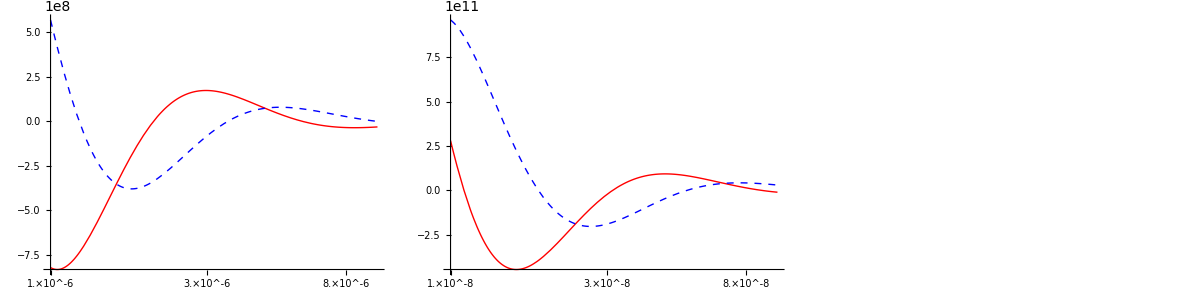

```mathematica
Clear["Global`*"]
z0=-0.5+3ⅈ;
f[t_]:=ⅇ^-t t^(z0-1);
f1=LogLinearPlot[{Re[f[t]],Im[f[t]]},{t,10^-6,10^-5},
Ticks->{{1. 10^-6,3. 10^-6,8. 10^-6},Automatic},
PlotStyle->{Red,Directive[Blue,Dashed]},PlotRange->All];
f2=LogLinearPlot[{Re[f[t]],Im[f[t]]},{t,10^-8,10^-7},
Ticks->{{1. 10^-8,3. 10^-8,8. 10^-8},Automatic},
PlotStyle->{Red,Directive[Blue,Dashed]},PlotRange->All];
f3=LogLinearPlot[{Re[f[t]],Im[f[t]]},{t,10^-11,10^-10},
Ticks->{{1. 10^-11,3. 10^-11,8. 10^-11},Automatic},PlotStyle->{Red,Directive[Blue,Dashed]},PlotRange->All];
Grid[{{f1,f2,f3}}]
```

如何得到定义域在整个复平面的 Γ(z) 函数?   ——   解析延拓。

在区域  Re z >0，有

Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+∫_0^1 ⅇ^-t t^(z-1)ⅆt     注意第二项在区域 Re z≤0 发散
=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)∫_0^1 t^k t^(z-1)ⅆt,         思考：这一步在 z 的哪个区域成立？
=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)1/(k+z)          第二项在 Re z<0 也解析了（孤立奇点之外）     
   到这步，居然得到一个在整个复平面上（除极点外）解析的函数，
                       当然这个函数在 Re z >0 时与 ∫_0^∞ ⅇ^-t t^(z-1)ⅆt 相同

令新函数

g(z)=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)1/(k+z)

观察函数 g(z) ：

第一项在全复平面解析，

第二项是个级数，该级数在除 z=0,-1,-2,... 外的全复平面"内闭一致收敛"，

即，第二项在全复平面除孤立奇点 z=0,-1,-2,... 外解析。

因而，g(z) 是一个在全复平面（除了一些孤立奇点外）的解析函数，并且，在 Re z>0 区域，g(z)=Γ(z）

故：g(z) 是第二类 Euler 积分 Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt 在整个复平面的解析延拓

现在就把 g(z) 定义为整个复平面上的 Γ 函数。这个新定义的 Γ 函数在全复平面（除了一些极点外）解析。

从而我们也就定义了一个在全复平面除孤立奇点（极点） z=0,-1,-2,... 外解析的函数：Γ(z)。

据延拓的唯一性，这种延拓是唯一的。利用其它方法做延拓，新的函数必与此相同。

这就是解析延拓的第一个用处：扩大函数的定义域，得到在一个更大的范围内（除一些孤立奇点外）的新解析函数。

我们还可以从 Γ 函数的延拓过程来理解 Ewald 求和：

G(z,r⃗)=-1/(4π)∑_s exp[ⅈ z |r⃗-(r⃗)_s|]/(|r⃗-(r⃗)_s|)exp[ⅈ k⃗· (r⃗)_s]

我们已知和函数 G(z,r⃗) 在某区域 D_1 ： Im z ≥0 内除一些孤立奇点外解析，但求和收敛缓慢。

在区域 D_1 的子区域 D_2： Im z >0 内，Ewald 导出一个新的表达式（解析函数），

那么这个新解析函数就在原区域 D_1：Im z ≥0 就等于原来的和函数 G(z,r⃗)。

为更好理解解析延拓，以下是解析延拓在 Gamma 函数和 Ewald 求和中的思路对比。

|                   Ewald 求和  |                       Gamma 函数
----- | ---------------------------   | ---------------------------
寻求： | 级数-1/(4π)∑_s exp[ⅈ z |r⃗-(r⃗)_s|]/(|r⃗-(r⃗)_s|)exp[ⅈ k⃗· (r⃗)_s]
在区域  Im z ≥0  快速收敛的表达式 |      一个在全平面 解析^*的 Gamma 函数
----- | --------------------------- | ---------------------------
已知： | 区域  Im z ≥0  级数收敛于
一个 解析^*函数： G(z,r⃗) | 存在这样一个在全平面 解析^*的函数
----- | --------------------------- | ---------------------------
做法： | 从 G(z,r⃗) 出发，在区域  Im z >0  
导出既快速收敛又在区域  Im z ≥0  
是 z 的解析^*函数的表达式
注意：推导仅在 Im z >0  成立
                得到的结果却在  Im z ≥0   解析^* | 从第二类 Euler 积分：∫_0^∞ ⅇ^-t t^(z-1)ⅆt 出发，
在区域  Re z >0  导出一个
在全平面 解析^*的函数：g(z)
注意：推导仅在  Re z >0  成立，
                 得到的结果 g(z) 却在全平面 解析^*
----- | --------------------------- | ---------------------------
结论： | 这个在区域  Im z ≥0  的 z 的 解析^*函数
表达式，即为所求的快速收敛表达式 | 这个在全平面 解析^*的函数：g(z)
即为所求的 Gamma 函数
----- | --------------------------- | ---------------------------

*： 此处的“解析^*”是指出孤立极点之外的解析函数。

当然，这并不表明，人们总是可以将在某些特定区域内导出的公式 随意“延拓” 到更大的区域。

也就是说，我们在特定区域  D_s证明了 A=B，那么等式 A=B 是否在更大的区域 D 也成立？

这里需要以下两个条件才能保证延拓的正确性：

原来的函数 A 和导出的函数 B 都在更大的区域解析。所谓解析延拓，就是解析才能延拓。

导出 A=B 的特定区域 D_s 与更大的区域 D 有重叠部分 S，或者在更大区域 D 内部证明：A=B

该重叠部分（D 内部） S 必须是：

一个区域、一条曲线，或者，至少是一个有聚点的点集（当然隐含了无穷多点的意思）。

对物理学家而言，第二点是必须的，第一点常被 take it for granted

### Gamma 函数的其他表示

Gamma 函数是我们接触的第一个特殊函数，作为一种特殊函数，它可以有许多不同的等价表示。

积分表达式 (BookChapterNumber.EquationNumbered) 仅仅是 Gamma 函数在某个特殊区域内（Re z>0）的一种表示，Gamma 函数还可以表示为：

Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt,     Re z >0, arg t=0,  积分表示（第二类 Euler 积分）
=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)1/(k+z),  已经过解析延拓 z ≠-n, n=0,1,2,...
=lim_(n→∞) (n!)/(z(z+1)(z+2)...(z+n))n^z=lim_(n→∞) (n! n^z)/((z)_(n+1)),    Euler 极限表示
1/(Γ(z))=z ⅇ^(γ z)(∏_(k=1))^∞(1+z/k)ⅇ^(-z/k)             Weierstrass 乘积表示
 Γ(z)=1/z(∏_(k=1))^∞[(1+z/k)^-1(1+1/k)^z]     Euler 乘积表示

γ=lim_(n→∞) (1+1/2+1/3+…+1/n-ln n)=0.5772156649... 称为 Euler-Mascheroni 常数，是一个无理数。

注：(z)_(n+1)≡z(z+1)(z+2)...(z+n) 称为 Pochhammer 符号

```mathematica
N[EulerGamma,80]
```

0.57721566490153286060651209008240243104215933593992359880576723488486772677766467

#### 几种表示的等价性 （略）

积分表示等价于极限表示

考虑含参数的积分

F(z,n)=∫_0^n (1-t/n)^n t^(z-1)ⅆt,    Re z>0, n 为正整数

当 n→∞ 时，

lim_(n→∞) F(z,n)=∫_0^∞ [lim_(n→∞) (1-t/n)^n]t^(z-1)ⅆt=∫_0^∞ ⅇ^-t t^(z-1)ⅆt

lim_(n→∞) F(z,n)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt

另一方面：F(z,n)=∫_0^n (1-t/n)^n t^(z-1)ⅆt=n^z∫_0^1 (1-u)^n u^(z-1)ⅆu,    其中令：t=u n

(I(n,z)=∫_0^1 (1-u)^n u^(z-1)ⅆu=(1-u)^n u^z/z|)_0^1+n/z∫_0^1 (1-u)^(n-1)u^z ⅆu=n/z I(n-1,z+1)

递推：I(n,z)=n/z I(n-1,z+1)=(n(n-1)⋯1)/(z(z+1)⋯(z+n-1))I(0,z+n)=(n!)/((z)_(n+1))

其中：I(0,z+n)=∫_0^1 u^(z+n-1)ⅆu=1/(z+n)，

Pochhammer 符号：(z)_n=(z(z+1)⋯(z+n-1))^(⏞^(n 个因子相乘))，(z)_0=1,  (z)_1=z,  (z)_2=z(z+1)

从而：F(z,n)=(n!)/((z)_(n+1))n^z

lim_(n→∞) F(z,n)=lim_(n→∞) (n!)/((z)_(n+1))n^z

联立 (BookChapterNumber.EquationNumbered) 与 (BookChapterNumber.EquationNumbered)：Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt=lim_(n→∞) F(z,n)=lim_(n→∞) (n!)/((z)_(n+1))n^z

极限表示等价于乘积表示

从极限表示出发：

Γ(z)=lim_(n→∞) (n! n^z)/((z)_(n+1))=lim_(n→∞) (n!)/(z(z+1)(z+2)...(z+n))n^z=lim_(n→∞) n^z/z(∏_(k=1))^n(1+z/k)^-1，

求倒数

1/(Γ(z))=lim_(n→∞) z/n^-z(∏_(k=1))^n(1+z/k)，  利用：n^-z=ⅇ^(-z ln n)及 ⅇ^(z(1+1/2+1/3+…+1/n))=(∏_(k=1))^n ⅇ^(z/k)
=zlim_(n→∞) ⅇ^((-ln n)z)ⅇ^(z(1+1/2+1/3+…+1/n))(∏_(k=1))^n(1+z/k)ⅇ^(-z/k)
=z lim_(n→∞) ⅇ^((1+1/2+1/3+…+1/n-ln n) z)(∏_(k=1))^n(1+z/k)ⅇ^(-z/k)
=z ⅇ^(lim_(n→∞) (1+1/2+1/3+…+1/n-ln n) z)lim_(n→∞) (∏_(k=1))^n(1+z/k)ⅇ^(-z/k)
=z ⅇ^(γ z)(∏_(k=1))^∞(1+z/k)ⅇ^(-z/k)=Weierstrass 乘积表示

其中：γ=lim_(n→∞) (1+1/2+1/3+…+1/n-ln n)=0.5772156619...

两种乘积表示的等价性，参见 Whittaker & Watson, A modern course of analysis, §12.11

### Gamma函数的基本性质

基本性质：

#### Γ(1)=1

z=1 代入积分表示 Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt 即得

#### Γ(z+1)=z Γ(z) 常被称为 Gamma 函数满足的差分方程

由极限表示

Γ(z+1)=lim_(n→∞) (n!)/((z+1)(z+2)...(z+n)(z+n+1))n^(z+1)
=lim_(n→∞) (n z)/(z+n+1)(n!)/(z(z+1)(z+2)...(z+n))n^z=z Γ(z)

由积分表示

(Γ(z+1)=∫_0^∞ ⅇ^-t t^z ⅆt=-t^z ⅇ^-t|)_0^∞+z∫_0^∞ ⅇ^-t t^(z-1)ⅆt
=z Γ(z)，  推导过程中利用了 Re z >0

以上仅在 Re z>0 区域证明 Γ(z+1)=z Γ(z)，

如果已经用(1.EquationNumbered)式：g(z)=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)1/(k+z)

定义了一个在全复平面除孤立奇点 z=0,-1,-2,... 外解析的函数 Γ(z)，

则等式：Γ(z+1)=z Γ(z)  左右两边均为解析函数，

我们在 Re z>0 区域证明其相等，根据解析延拓原理，

就证明了它们在整个解析区域（即除 0 与负整数外的整个复平面）相等。

有的教材仅仅利用积分表示：（第二类 Euler 积分）

∫_0^∞ ⅇ^-t t^(z-1)ⅆt   定义一个在 Re z>0 区域解析的函数 Γ(z)，

再把该解析函数在 Re z>0 区域的性质：Γ(z+1)=z Γ(z)   推广到全平面，进而通过

Γ(z)=Piecewise[{{∫_0^∞ ⅇ^-t t^(z-1)ⅆt,, Re z>0}, {(Γ(z+1))/z,, -1<Re z≤0, z≠0}}] 定义一个在 Re z>-1区域除 z=0外解析的函数，

由此定义的函数在 z=0 是单极点，且留数 Res Γ(0)=Γ(1)=1。

类似地，进一步定义

Γ(z)=Piecewise[{{∫_0^∞ ⅇ^-t t^(z-1)ⅆt,, Re z>0}, {(Γ(z+2))/(z(z+1)),, -2<Re z≤0, z≠0,-1}}] 则该函数在 Re z>-2区域除 z=0, -1外解析

且在单极点 z=0, -1 的留数为 Res Γ(0)=1, Res Γ(-1)=-1

以此类推，可以将由第二类 Euler 积分 (BookChapterNumber.EquationNumbered) ：∫_0^∞ ⅇ^-t t^(z-1)ⅆt  定义的 Gamma 函数延拓到整个复平面，延拓的函数除单极点 z=0, -1, -2, … 外在全平面解析，Res Γ(-n)=(-1)^n/(n!)

由此定义的 Γ 函数与 (BookChapterNumber.EquationNumbered) 式的 g(z) ：g(z)=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)1/(k+z)

当然一致，因为解析延拓是具有唯一性。它们都在整个复平面除单极点 0 与负整数点之外解析。

且在单极点的留数：Res Γ(-n)=(-1)^n/(n!)。

▲  用 (BookChapterNumber.EquationNumbered) 式的 g(z) 延拓较易接受，因为先延拓成解析函数，

然后在解析区域的子区域证明等式：Γ(z+1)=z Γ(z)

将此等式延拓到整个解析区，思路较为清晰

若由第二类 Euler 积分 (BookChapterNumber.EquationNumbered) 定义 Re z>0 区域解析的解析函数 Γ(z)，

再用仅在  Re z>0 区域证明了的等式：Γ(z+1)=z Γ(z)

将 Γ(z)延拓到 Re z ≤0 的区域：Γ(z)=(Γ(z+n+1))/(z(z+1)(z+2)…(z+n))

理解上似乎有些跳跃。（结果当然是一致的）

但易于记住  Γ(z) 仅有单极点 z=-n, (n=0,1,2,...)  且留数 Res Γ(-n)=(-1)^n/(n!)

推论：对正整数 n，Γ(n)=(n - 1)! ，故 Gamma 函数也被称为阶乘函数，

或反过来理解，把定义域为正整数的函数（阶乘）拓展为一个定义域在复平面上的复变函数

推论：对负整数 -n，可理解为

1/(Γ(-n))=1/((-n-1)!)，而：1/(Γ(-n))=lim_(z→-n) 1/(Γ(z))=lim_(z→-n) (z(z+1)...(z+n))/(Γ(z+n+1))=0

1/(Γ(-n)) =1/((-n-1)!)=0     ——  负整数的阶乘的倒数为 0。

#### Γ(z)Γ(1-z)=π/(sin π z) 也称 互余宗量关系

此等式最简单的证明是在 0<x=Re z<1 的实轴上利用积分表示通过变量代换进行。

Γ(x)Γ(1-x)=∫_0^∞ ⅇ^-t t^(x-1)ⅆt∫_0^∞ ⅇ^-s s^-x ⅆs=∫_0^∞ ∫_0^∞ (ⅇ^(-(s+t))(t/s))^x 1/t ⅆtⅆs

变量代换：ξ=s+t,  η=t/s,  J=(∂(s,t))/(∂(ξ,η))=|(∂s)/(∂ξ) | (∂s)/(∂η)
(∂t)/(∂ξ) | (∂t)/(∂η)|=ξ/(η+1)^2,   ⅆtⅆs=Jⅆξ ⅆη

Γ(x)Γ(1-x)=∫_0^∞ ∫_0^∞ ⅇ^-ξ η^x(1+η)/(ξ η)(ξ/(1+η)^2)^(⏞^(Jacobi 行列式 J))ⅆξⅆη=∫_0^∞ ⅇ^-ξ ⅆξ(∫_0^∞ η^(x-1)/(η+1)ⅆx)^(⏞^(§ 5.2例题))=π/(sin πx)

以上在 0<x<1的一段实轴证明了等式，又由于等式两边均为解析函数，据解析延拓原理，二者在解析区域相等。

```mathematica
Clear["Global`*"]
eq1=ξ-(s+t);
eq2=η-t/s;
r=Solve[{eq1==0,eq2==0},{s,t}];
r1=r[[1]]
Jm={{D[s/.r1,ξ],D[s/.r1,η]},{D[t/.r1,ξ],D[t/.r1,η]}};
J=Simplify[Det[Jm]]
f[s_,t_]:=ⅇ^(-(s+t))(t/s)^x 1/t
Integrate[J *f[s,t]/.r1,{ξ,0,∞},{η,0,∞}]
```

{s→ξ/(1+η),t→ξ-ξ/(1+η)}

ξ/(1+η)^2

π Csc[π x]

此等式的另一种证明方法是利用 Weierstrass 乘积表示

Γ(z)Γ(-z)=[z^-1 ⅇ^(-γ z)(∏_(k=1))^∞(1+z/k)^-1 ⅇ^(z/k) ]×[-z^-1 ⅇ^(γ z)(∏_(k=1))^∞(1-z/k)^-1 ⅇ^(-z/k)]
=-1/z^2(∏_(k=1))^∞(1-z^2/k^2)^-1,   利用：sin z=z(∏_(k=1))^∞(1-z^2/(k^2 π^2))
=-π/(z sin π z),  再利用  Γ(α)=(Γ(1+α))/α,   α=-z

-π/(z sin π z)=Γ(z)Γ(-z)=Γ(z)(Γ(1-z))/-z  ⟹   Γ(z)Γ(1-z)=π/(sin π z)

看上去很美，但如何证明 sin z 的无穷乘积表达式？

涉及将一个函数展为无限项的乘积，参见以下“两个定理”一节

推论：令 z=1/2,  Γ(z)Γ(1-z)=π/(sin π z)     ⟹     Γ(1/2)=√π

Gamma函数在全平面无零点

Γ(z)Γ(1-z)=π/(sin π z)≠0,    若 z=z_0 是 Gamma函数的零点， Γ(z_0)=0, 则

Γ(z_0)Γ(1-z_0)=π/(sin π z_0)≠0  必导致  Γ(1-z_0)=∞  ⟹  1-z_0=-n  ⟹ z_0=n+1  ⟹  Γ(z_0)=n!, 矛盾。

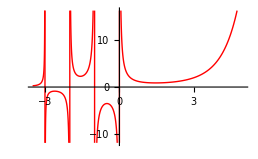

```mathematica
Plot[Gamma[x],{x,-3.5,5},PlotStyle->{Red,Thick}]
```

#### Γ(2z)=2^(2z-1)π^(-1/2)Γ(z)Γ(z+1/2) 也称 Legendre 倍乘公式

证明：见 Gauss 乘法定理的证明。

#### Γ(n z)=(2π)^((1-n)/2)n^(n z-1/2) Γ(z)Γ(z+1/n)Γ(z+2/n)⋯Γ(z+(n-1)/n) 也称 Gauss 乘法定理

证明：定义函数： ϕ(z)=(n^(n z) Γ(z)Γ(z+1/n)Γ(z+2/n)⋯Γ(z+(n-1)/n))/(Γ(n z))=(n^(n z) (∏_(k=0))^(n-1)Γ(z+k/n))/(Γ(n z))

实际上，ϕ(z)是将 Gauss 乘法定理中与 z 有关的部分移到一边而得。以下证明 ϕ(z) 是与 z 无关的常数。

由 Gamma 函数的极限表示：Γ(z)=lim_(n→∞) (n! n^z)/((z)_(n+1))=lim_(n→∞) n/(n+z)((n-1)! n^z)/((z)_n)=lim_(n→∞) ((n-1)! n^z)/((z)_n)

ϕ(z)=(n^(n z) (∏_(k=0))^(n-1)lim_(m→∞) ((m-1)! m^(z+k/n))/((z+k/n)_m))/(lim_(m→∞) ((m-1)! m^(n z))/((n z)_m)),   分子有 n m 项 (z+α)形式乘积
=(n^(n z)lim_(m→∞) (∏_(k=0))^(n-1)((m-1)! m^(z+k/n))/((z+k/n)(z+k/n+1)(z+k/n+2)⋯(z+k/n+m-1)))/(lim_(m→∞) ((n m-1)! (n m)^(n z))/((n z)_(n m)))
=lim_(m→∞) (((n^(n z) [(m-1)!])^n m^(n z+(n-1)/2))/((z)(z+1)⋯(z+m-1)(z+1/n)(z+1/n+1)⋯(z+1/n+m-1)⋯(z+(n-1)/n)(z+(n-1)/n+1)⋯(z+(n-1)/n+m-1)))/(((n m-1)! (n m)^(n z))/((n z)(n z+1)(n z+2)⋯(n z+n m-1)))
=lim_(m→∞) ([(m-1)!]^n m^((n-1)/2))/((n m-1)!) ((n z)(n z+1)(n z+2)⋯(n z+n m-1))/((z)(z+1)⋯(z+m-1)(z+1/n)(z+1/n+1)⋯(z+1/n+m-1)⋯(z+(n-1)/n)⋯(z+(n-1)/n+m-1))
=lim_(m→∞) ([(m-1)!]^n m^((n-1)/2))/((n m-1)!)n^(n m)         终于证明了 ϕ(z) 与 z 无关！

接下来就好办了，只要求出 ϕ(z) 的值就可以了。既然 ϕ(z) 与 z 无关，则可任选一 z 值求之。

取 z=z_0=1/n 求之：

(ϕ(z_0)=(n^(n z) (∏_(k=0))^(n-1)Γ(z+k/n))/(Γ(n z))|)_(z=z_0)=(n^(n/n) Γ(1/n)Γ(2/n)Γ(3/n)⋯Γ(1))/(Γ(1))=n Γ(1/n)Γ(2/n)⋯Γ((n-2)/n)Γ((n-1)/n)>0

ϕ^2(z_0)=n^2(∏_(k=1))^(n-1)[Γ(k/n)Γ(1-k/n)]=n^2(∏_(k=1))^(n-1)π/(sin(k π)/n)=(n^2 π^(n-1))/(sin π/n sin (2π)/n⋯sin ((n-1)π)/n)=n (2π)^(n-1)

其中利用了： Γ(z)Γ(1-z)=π/(sin π z)  及  sin π/n sin (2π)/n⋯sin ((n-1)π)/n=n/2^(n-1)  （第一章例题）

整理即得：ϕ(z)=(n^(n z) Γ(z)Γ(z+1/n)Γ(z+2/n)⋯Γ(z+(n-1)/n))/(Γ(n z))=ϕ(z_0)=(2π)^((n-1)/2)n^(1/2)

⟹    Gauss乘法定理：Γ(n z)=(n^(n z-1/2)(2π))^((1-n)/2) Γ(z)Γ(z+1/n)Γ(z+2/n)⋯Γ(z+(n-1)/n)

#### 补充：两个定理

亚纯函数的极点展开（既非Taylor展开，亦非Laurent展开）

亚纯函数 (meromorphic function)：除孤立极点（极点，不是本性奇点）之外解析的函数，例如：(sin z)/(cos z)

极点展开定理：设亚纯函数 f(z) 在复平面上只有非零单极点 a_k≠0，其中 |a_1|<|a_2|<⋯，Res f(a_k)=b_k,

并且在包围前 n 个单极点的半径为 R_n 的圆周 C_n 上，函数满足 lim_(n→∞) |(f(z))/R_n|=0，其中 lim_(n→∞) R_n=∞，

则 f(z)可表为极点展开形式：f(z)=f(0)+(∑_(k=1))^∞(b_k/(z-a_k)+b_k/a_k)

证明：此定理也称 Mittag–Lefﬂer 定理。

展开式不同于Taylor展开或Laurent展开，而是在各单极点上展开。

观察积分：I_n=∳_C_n (f(ξ))/(ξ(ξ-z))ⅆξ，被积函数：φ(ξ)=(f(ξ))/(ξ(ξ-z))

I_n=2π ⅈ ∑_m Res φ(ξ_m)=2π ⅈ [-(f(0))/z+(f(z))/z+(∑_(k=1))^n b_k/(a_k(a_k-z))]

其中：φ(ξ)=(f(ξ))/(ξ(ξ-z)) 在 C_n 内有 (n+2)个单极点：ξ_m=0, z, 及 a_k, k=1,2,…,n

以下证明 n→∞ 和 R_n→∞ 时，有 I_n→0。

利用 lim_(n→∞) |(f(z))/R_n|=0，可导得：

|I_n|≤∳_C_n (|f(ξ)|)/(|ξ||(ξ-z)|)|ⅆξ|≤ ∳_C_n (|f(ξ)/R_n|)/(|(ξ-z)|)|ⅆξ|≤ε (2π R_n)/(|R_n|-|z|)≤ M ε，即：lim_(n→∞) I_n=0

lim_(n→∞) I_n=0代入 (BookChapterNumber.EquationNumbered)即得：f(z)=f(0)-(∑_(k=1))^n(z b_k)/(a_k(a_k-z))=f(0)+(∑_(k=1))^∞(b_k/(z-a_k)+b_k/a_k)。

整函数的乘积展开（函数表为无穷项之积，而非无穷项之和）

整函数 (entire function)：在整个复平面上（不含无穷远点）解析的函数，例如：sin z, cos z, (sin z)/z

乘积展开定理：设整函数 f(z) 在复平面上只有非零的一阶零点 a_k≠0, 其中 |a_1|<|a_2|<⋯，

并且在包围前 n 个零点的半径为 R_n 的圆周 C_n 上，函数的对数导数 h(z)=(f'(z))/(f(z))满足lim_(n→∞) |(h(z))/R_n|=0，

其中 lim_(n→∞) R_n=∞，则 f(z)可表为乘积展开形式：f(z)=f(0)exp[(z f'(0))/(f(0))](∏_(k=1))^∞(1-z/a_k)ⅇ^(z/a_k)

证明：因为整函数 f(z)只有一阶零点，其对数导数 h(z)=(f'(z))/(f(z))只有单极点，是亚纯函数。

在 f(z)的任意一个一阶零点 a_k 的邻域均有：f(z)=(z-a_k)g_k(z),  g_k(z)解析且 g_k(a_k)≠0

在 a_k 邻域, h(z)=(f'(z))/(f(z))=([(z-a_k)g_k(z)]')/((z-a_k)g_k(z))=1/(z-a_k)+(g'_k(z))/(g_k(z))，

故 f(z)的一个一阶零点 a_k 对应于其对数导数 h(z)=(f'(z))/(f(z)) 的一个留数 b_k 等于 1的单极点

这步证明：Res h(a_k)=b_k=1，在上一章“对数留数与Rouche定理”一节已经证过。

h(z) 又满足纯函数极点展开定理的条件，故：h(z)=h(0)+(∑_(k=1))^∞(b_k/(z-a_k)+b_k/a_k)，且所有 b_k=1

故：(f'(z))/(f(z))=(f'(0))/(f(0))+(∑_(k=1))^∞(1/(z-a_k)+1/a_k)，   注意 f(0)≠0 ，因为f(z) 在复平面只有非零的一阶零点

上式两边同时从 z=0 到 z 积分

左=∫_0^z (f'(ξ))/(f(ξ))ⅆξ=ln f(z)-ln f(0)

右=(f'(0))/(f(0))z+(∑_(k=1))^∞[ln (z-a_k)-ln(-a_k)+z/a_k]

▲  注意被积函数含有奇点，积分与路径有关，原函数是多值函数，如：ln (z-a_k)

但接着求指数函数，多值性自动消失

上式两边同取指数：f(z)=f(0)exp[(f'(0))/(f(0))z](∏_(k=1))^∞(a_k-z)/a_k ⅇ^(z/a_k)      函数表为无穷乘积

实例：

f(z)=(sin z)/z 满足乘积展开定理的条件：

仅有非零的一阶零点 a_k=k π，k=±1, ±2, ±3, …

h(z)=(f'(z))/(f(z))=-1/z+(cos z)/(sin z) 在 R_n ⅇ^(ⅈ θ)上且 R_n→∞ 满足 (h(R_n ⅇ^(ⅈ θ)))/R_n→0

再利用：f(0)=1,  f'(0)=0,

即得：(sin z)/z=(∏_(k=1))^∞ ((1-z/(k π))ⅇ^(z/k π))^(⏞^(对应于 k=1,2,3,...))   ((1-z/(-k π))  ⅇ^(-z/k π))^(⏞^(对应于 k=-1, -2, -3,...))  ⟹     sin z=z(∏_(k=1))^∞(1-z^2/(k^2 π^2))

f(z)=cos z 满足乘积展开定理的条件：

一阶零点 a_k=(k-1/2) π，k=0, ±1, ±2,  ±3, …

h(z)=(f'(z))/(f(z))=-(sin z)/(cos z) 在 R_n ⅇ^(ⅈ θ)上且 R_n→∞ 满足 (h(R_n ⅇ^(ⅈ θ)))/R_n→0

故：cos z=(∏_(k=1))^∞(1-z/((k-1/2) π))(1+z/((k-1/2) π))    ⟹   cos z=(∏_(k=1))^∞(1-z^2/((k-1/2)^2 π^2))

亚纯函数的极点展开和整函数的乘积展开因为公式复杂，只需了解有这样的展开方式即可。

整函数的对数导数是仅有单极点的亚纯函数，例如：亚纯函数 (sin z)/(cos z)是整函数 -cos z的对数导数

对数导数可用于将无穷和化为无穷积

Γ 函数在全空间无零点，1/(Γ(z)) 是整函数，f(z)=1/(z Γ(z)) 满足整函数的乘积展开条件，

故可表为连乘积形式： f(z)=f(0)exp[(f'(0))/(f(0))z](∏_(k=1))^∞(a_k-z)/a_k ⅇ^(z/a_k)

此即 Weierstrass 乘积表示：1/(Γ(z))=z ⅇ^(γ z)(∏_(k=1))^∞(1+z/k)ⅇ^(-z/k)

由 sin z=z(∏_(k=1))^∞(1-z^2/(k^2 π^2)) 可导得诸如：lim_(k→∞) ((k!)^2 2^(2k+1))/((2k)! √(2k+1))=√(2π) 貌似很神奇的等式。

```mathematica
Limit[((n!)^2 2^(2n+1))/((2n)!√(2n+1)),n->∞]
```

√(2 π)

### Gamma 函数的围道积分表示及渐近表达式：

#### Gamma 函数的围道积分表示

∫_C ⅇ^-ζ ζ^(z-1)ⅆζ=(ⅇ^(ⅈ z 2π)-1)Γ(z) ,         Γ(z)=-1/(2ⅈ sin z π)∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ

我们已经了解：

第二类 Euler 积分(BookChapterNumber.EquationNumbered) 式：Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt  仅在 Re z>0 区域收敛且解析，表示 Gamma 函数。

通常，人们还需要更为有效的围道积分表示。希望得到对任意 z 皆可用的积分表示。

为此，考虑如下围道积分，其中 z 为复变量

F(z)=∫_C ⅇ^-ζ ζ^(z-1)ⅆζ，积分围道 C 如下图绿线所示，被积函数 f(ζ,z)=ⅇ^-ζ ζ^(z-1)

比较第二类 Euler 积分中的被积函数：ⅇ^-t t^(z-1)

-Graphics-

积分围道 C 从正实轴上缘的 ∞ 出发，左行至原点附近，绕原点一周到达正实轴下缘，再右行到正实轴下缘的 ∞ 处。

被积函数 f(ζ,z)=ⅇ^-ζ ζ^(z-1)是多值函数，枝点为 ζ=0 与 ∞，割线如上图红线，围道 C 不穿过割线。

做了割线之后，f(ζ,z)就成为单值解析函数（除 ζ=0, ∞ 是枝点、非孤立奇点），积分围道在解析区可连续变形。

因此，可将积分路径变化为：C ⟶ L_1+C_r+L_2，其中 L_1 (L_2) 沿割线上（下）岸，C_r 是半径为 r 的圆弧。

F(z)=∫_C ⅇ^-ζ ζ^(z-1)ⅆζ=∫_(L_1+C_r+L_2) ⅇ^-ζ ζ^(z-1)ⅆζ，

第二类 Euler 积分：Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt  相当于 r→0 时的 L_1 的反向

C_r ：ζ=r ⅇ^(ⅈ θ)，故积分可化为本节定理一形式的积分，∫_C_r ⅇ^-ζ ζ^(z-1)ⅆζ=∫_0^(2π) ⅇ^(- r (cos θ + ⅈ sin θ)) (r ⅇ^(ⅈ θ))^z ⅈ ⅆθ

易证它满足定理一的条件，故该积分：∫_C_r   收敛于一个解析函数。注意这里并没有让 r→0。

L_1 或 L_2 ：因为在实轴，可化为本节定理二形式的积分：∫_a^∞ …  ⅆt

易证明它满足定理的条件，积分也收敛于一个解析函数。

例如，在 L_1：∫_L_1 f(ζ,z)ⅆζ=-∫_r^∞ ⅇ^-t t^(z-1)ⅆt  ⟹^(取 r =1)   (1.EquationNumbered) 式第二项，全平面解析。

从而积分 F(z) =∫_C f(ζ,z)ⅆζ=∫_C ⅇ^-ζ ζ^(z-1)ⅆζ  在全复 z 平面收敛并代表一个解析函数。

▲   在证明 F(z) 解析这一结论时，C_r 的半径 r  并不趋于 0，实际上，

这时的 r 必须是有限的，例如可取 r=1。

取 r→0 反而难以证明 F(z) 解析。

接着，我们求这个全复平面解析的函数 F(z) 与 Gamma 函数 Γ(z) （存在单极点）之间的关系。

-Graphics-

规定在割线上岸：θ≡arg ζ=0，因而在割线下岸：θ≡arg ζ=2π

L_1：ζ=t ⅇ^(ⅈ 0), ∫_L_1 f(ζ,z)ⅆζ=∫_∞^r ⅇ^-t t^(z-1)ⅆt=-∫_r^∞ ⅇ^-t t^(z-1)ⅆt=-I

L_2：ζ=t ⅇ^(ⅈ 2π), ∫_L_2 f(ζ,z)ⅆζ=∫_r^∞ ⅇ^-t t^(z-1)ⅇ^(ⅈ z 2π)ⅆt=ⅇ^(ⅈ z 2π)I，  这里     I=((∫_r^∞)^)_ ⅇ^-t t^(z-1)ⅆt

C_r：利用小圆弧引理？      要用小圆弧引理，就必须要有  r→0，

F(z) 能否视为 r→0 时的积分？可以，因为积分路径可在被积函数的解析区任意变形（Cauchy 定理的推论）。

在证明函数解析时，可取 r=1，而在求函数值时，却要让 r→0，此所谓“识时务者为俊杰”。

因此，令 r→0 ，即可利用小圆弧引理。

小圆弧引理中的 k= lim_(ζ→0) ζ f(ζ,z)=lim_(ζ→0) ⅇ^-ζ ζ^z→^(当 Re z >0 时) 0，    ∫_C_r f(ζ,z)ⅆζ=0  if  Re z>0

当然 r→0时，lim_(r→0) I=lim_(r→0) ∫_r^∞ ⅇ^-t t^(z-1)ⅆt=Γ(z)   ⟹  ∫_L_1 +∫_L_2=(ⅇ^(ⅈ z 2π)-1)Γ(z)

注意：仅在 r→0 时，在 L_1 与 L_2 的积分才能与 Γ 函数相关联，C_r 的积分才能利用小圆弧引理。

而在证明 F(z) 解析时， r 是有限的；仅仅在要将 F(z) 与 Γ 函数相关联时，才需要用到   r→0。

综合上述讨论：当 Re z >0 时，取 r→0 的极限，lim_(r→0) I=Γ(z)

F(z)=∫_C ⅇ^-ζ ζ^(z-1)ⅆζ=∫_L_1 +∫_L_2 +∫_C_r=(ⅇ^(ⅈ z 2π)-1)Γ(z),

即：∫_C ⅇ^-ζ ζ^(z-1)ⅆζ=(ⅇ^(ⅈ z 2π)-1)Γ(z)    —— 此式在全复平面成立

我们虽然仅仅在 Re z >0 时，证明了F(z)与 Gamma 函数的关系，但在整个复平面，上式左右两边都是解析函数

（注意  z =0 或负整数是 Γ(z)的单极点，是 (ⅇ^(ⅈ z 2π)-1)Γ(z)的可去奇点，上式右边依然是解析函数）

依据解析延拓原理，上式在整个复平面内成立。只不过当 z 等于整数时，上式无法求出 Γ(z)。

这里可看到复围道积分与解析延拓思想的妙处：

在需要证明解析时，取圆弧半径  r 有限，例如可取 r=1

在需要与 Γ 函数相关联时令 r→0并仅在 Re z>0区域证明等式。

思考：对 Re z ≤0，小圆弧段的积分是发散的，这是否与 F(z) =∫_C ⅇ^-ζ ζ^(z-1)ⅆζ 在全平面解析矛盾？

（答：没有矛盾，因为这时的 I=∫_r^∞ ⅇ^-t t^(z-1)ⅆt 在 r→0时也发散，这些发散项相消，故 F(z)依然解析。）

从以上的证明看到，规定割线上下岸 arg ζ 分别为 0 与 2π，则 ∫_L_1 +∫_L_2=(ⅇ^(ⅈ z 2π)Γ(z))_(⏟_(来自 L_2 的积分)) -  (Γ(z))_(⏟_(来自 L_1))

图样图森破的想法：

若规定割线上下岸 arg ζ 分别为 ∓π，似乎能得到 更为对称形式：∫_L_1 +∫_L_2∼(ⅇ^(ⅈ z π)-ⅇ^(- ⅈ z π))Γ(z)∼ sin z π Γ(z)

但显然在割线上岸不能规定 arg ζ=±π

——  why?  答：因为在上岸 ζ 矢量与正实轴平行，arg ζ 只能是偶数倍的 π。

不过，倒是可以规定在割线上岸 arg(-ζ)=-π，那么割线下岸  arg(-ζ)=π。

-Graphics-          规定上岸 arg(-ζ)=-π
那么下岸 arg(-ζ)=π_
若规定上岸 arg(-ζ)=π
则下岸 arg(-ζ)=3π，有失去对称了

为此，考虑： G(z)=∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ,   比较：F(z)=∫_C ⅇ^-ζ ζ^(z-1)ⅆζ

积分围道同 F(z)如上图，被积函数 g(ζ,z)=(ⅇ^-ζ(-ζ))^(z-1)。

与 F(z)的区别在于：可以规定割线上岸  θ'≡arg(- ζ)=-π，从而下岸 θ'=π

-ζ 是从 ζ 到 0 的矢量，当 ζ 在 L_1 时，矢量 -ζ 的指向从右到左，辐角可定义为奇数倍的 π。

L_1：-ζ=t ⅇ^(- ⅈ π), ∫_L_1 g(ζ,z)ⅆζ=∫_∞^r ⅇ^-t t^(z-1)ⅇ^(-ⅈ (z-1) π)ⅆt=ⅇ^(-ⅈ z π)∫_r^∞ ⅇ^-t t^(z-1)ⅆt=ⅇ^(-ⅈ z π)I

L_2：-ζ=t ⅇ^(ⅈ π), ∫_L_2 f(ζ,z)ⅆζ=∫_r^∞ ⅇ^-t t^(z-1)ⅇ^(ⅈ (z-1) π)ⅆt=-ⅇ^(ⅈ z π)I

的确，形式上对称了（注意小圆弧段的积分对 Re z >0 仍为 0），从而：

G(z)=∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ=(ⅇ^(-ⅈ z π)-ⅇ^(ⅈ z π))Γ(z),

即：Γ(z)=-1/(2ⅈ sin z π)∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ           ——  注意蓝色部分全复平面解析

上式称为 Hankel 公式。其本质在于使 Γ 函数的奇点以 1/(sin π z) 形式原形毕露。原来是单极点。

那么，z 为正整数时，分母也为零？是奇点吗？

答：z 为正整数是∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ 的零点（试证之），自然不是 Γ(z) 的奇点

Hankel 公式可两边同乘以 Γ(1-z)，左边利用互余宗量关系：Γ(z)Γ(1-z)=π/(sin z π)

得：Γ(z)Γ(1-z)=-(Γ(1-z))/(2ⅈ sin z π)∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ     ⟹^互余宗量关系    1=Γ(1-z) ⅈ/(2 π)∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ

⟹^(1-z = z')     1/(Γ(z))=ⅈ/(2 π)∫_C (ⅇ^-ζ(-ζ))^-z ⅆζ

此式就真的可用于表示任意 z 值（包括整数）的 Gamma 函数。

并且，因为此式的右边是全平面无奇点的解析函数，故可知 Γ(z)无零点。

#### Gamma 函数的渐近展开（|z|→∞ 时的近似表达式），也称 Stirling 公式

|z| ≫1 且 |arg z|<π  时， Γ(z) ∼  z^(z-1/2)ⅇ^-z √(2π)；

这就是统计物理中常用的：   N≫1时，N!  ∼ √(2π N) (N/ⅇ)^N  ~  (N/ⅇ)^N

证明：在此仅给出实数 z=x≫1时的证明，复数情形的证明将在讨论课中介绍。

Γ(x+1)=∫_0^∞ ⅇ^-u u^x ⅆu=∫_0^∞ ⅇ^(-u+x ln u)ⅆu,   令 u=x t,  则：

Γ(x+1)=x∫_0^∞ ⅇ^(-x t+x ln t+x ln x)ⅆt     ⟹^(Γ(x+1) = x Γ(x))     Γ(x)=x^x∫_0^∞ ⅇ^(x (ln t- t))ⅆt

以上几步用于把积分化成如右形式：f(x) = ∫_a^b h(t)ⅇ^(x g(t))ⅆt

如何计算这种形式的积分在 x≫1时的渐近表达式?

分析：如果函数 g(t)在积分区间 [a,b]的某一点 t_0 有极大值，

则在x→+∞时，经指数函数“放大”，函数 e^(x g(t))必有极其陡峭的峰。

若函数 g(t)只有这一个极大值且 h(t) 是缓变函数，

那么 x→+∞ 时的积分值主要由 t_0 附近的一小段所贡献。

因此，可取这一小段的积分值作为 f(x) 在 x→+∞ 时的渐近表示。

比较  Γ(x)=x^x∫_0^∞ ⅇ^(x (ln t- t))ⅆt  与 f(x) = ∫_a^b h(t)ⅇ^(x g(t))ⅆt

积分中：h(t)=1, g(t)=ln t-t  在 t=t_0=1有极大值，因此在 x≫1时积分可以用 t_0=1邻域的一段积分近似。

下图展示：g(t)=ln t-t 在 t=1处有一极大值，但变化缓慢

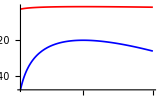

```mathematica
Clear["Global`*"]
g[t_]:=Log[t]-t;
amp=20;
Plot[{g[t],amp g[t]},{t,1/10,2},PlotRange->All,
           PlotStyle->{{Red,Thickness[0.0075]},{Blue,Thickness[0.0075]}}]
```

下图展示：当 x ≫ 1时，函数 e^(x g(t))在 t=1出现极其陡峭的峰。从而可在 t=1 邻域求积分近似值

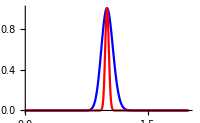

```mathematica
x1=200;
x2=2000;
s1=Exp[x1 g[1]];  (* 这步用于将最大值归一 *)
s2=Exp[x2 g[1]];
fig1=Plot[{Exp[x1 g[t]]/s1,Exp[x2 g[t]]/s2},{t,0,2},PlotRange->All,PlotPoints->100,PlotStyle->{Blue,Red},ImageSize->{200,200},
                        PlotLegends->{Style["ⅇ^(200 (ln t - t))",Italic,FontFamily->Times,15],Style["ⅇ^(2000 (ln t - t))",Italic,FontFamily->Times,15]}]
```

f(x) = ∫_a^b h(t)ⅇ^(x g(t))ⅆt 形式的积分，   Γ(x)=x^x∫_0^∞ ⅇ^(x (ln t- t))ⅆt

I=∫_0^∞ ⅇ^(x (ln t- t))ⅆt,    x ≫1 时，被积函数 ⅇ^(x (ln t- t))在 t_0=1处出现陡峭峰，故可在 t_0 邻域计算积分近似值
∼ ∫_(t_0-δ)^(t_0+δ) ⅇ^(x g(t))ⅆt,   因为积分在 t_0 的邻域进行，可对 g(t) 在 t_0 邻域作 Taylor 展开，仅保留两项，
∼∫_(t_0-δ)^(t_0+δ) ⅇ^(x [-1-1/2(t-1)^2-...])ⅆt,     因为偏离 t_0 点时，指数函数下降极为陡峭，积分区间可拓展为 -∞ 到 ∞        
∼∫_(-∞)^∞ ⅇ^(x [-1-1/2(t-1)^2])ⅆt,         现在被积函数相当简单，积分就可轻易计算了
=ⅇ^-x∫_(-∞)^∞ ⅇ^(-x/2(t-1)^2)ⅆt =ⅇ^-x √((2π)/x),    其中利用了：∫_(-∞)^∞ ⅇ^(-x/2 u^2)ⅆu=√((2π)/x)

从而：x≫1时， Γ(x)=x^x∫_0^∞ ⅇ^(x (ln t- t))ⅆt  ∼x^x I      ⟹    Γ_^(x)∼x^(x-1/2)ⅇ^-x(√(2π))^,   x≫1

数学思想：将一个积分化为：  f(x) = ∫_a^b h(t)ⅇ^(x g(t))ⅆt   形式，在 g(t)的极大值附近展开保留两项

x! =Γ(x+1)=∫_0^∞ u^x ⅇ^-u ⅆu=∫_0^∞ 1 ⅇ^(x ( ln u -u/x))ⅆu           化成上述形式：∫_a^b h(u)ⅇ^(x g(u))ⅆu

接着，将缓变函数（此处为 1）提出积分号，再将剩余的被积函数取对数，

在对数的极大值处 Taylor 展开，仅保留两项，代回原被积函数

g(u)=ln ⅇ^(x ( ln u -u/x))=x ln u -u  在极大值 u=x 处 Taylor 展开

g(u)≈-x-x ln x-1/(2x)(u-x)^2     代回原被积函数得：ⅇ^(g(u))=ⅇ^(-x-x ln x-1/(2x)(u-x)^2)

Γ(x+1)=∫_0^∞ u^x ⅇ^-u ⅆu=∫_0^∞ x^x ⅇ^-x ⅇ^(-1/(2x)(u-x)^2)ⅆu

此即统计力学中用到的：

n! =∫_0^∞ t^n ⅇ^-t ⅆt ≈∫_0^∞ n^n ⅇ^-n ⅇ^(-(t-n)^2/(2n))ⅆt      令 y=t-n
=∫_-n^∞ n^n ⅇ^-n ⅇ^(-y^2/(2n))ⅆy         因为 n 很大，主要贡献来自 |y|≤n   
≈n^n ⅇ^-n(∫_(-∞)^∞ ⅇ^(-y^2/(2n))ⅆy)_(⏟_高斯型积分) =n^n ⅇ^-n √(2π n)=√(2π n) (n/e)^n

n!≈√(2π n) (n/e)^n                 统计物理中常用

近似与严格结果的比较：Γ_^(x+1)∼(x+1)^x ⅇ^(-(x+1))(√(2π(x+1)))^,   x≫1

或上式令：x=n+1  得：   n! ~ √(2π (n+1))((n+1)/ⅇ)^n,    n≫1

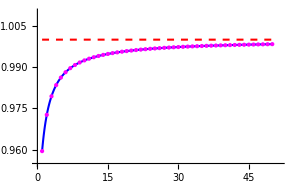

```mathematica
Clear["Global`*"]
g[x_]=√(2π)(x+1)^(x+1-1/2)ⅇ^(-x-1)/Gamma[x+1];
g1=Plot[{1,g[x]},{x,1,50},PlotRange->{{0,51.5},{0.955,1.01}},
               AxesOrigin->{0,0.955},
               PlotStyle->{{Red,Thickness[0.005],Dashed},{Blue,Thickness[0.005]}}];
tbl=Table[(√(2π (n+1)))/ⅇ ((n+1)/ⅇ)^n/n!,{n,1,50}];
g2=ListPlot[tbl,PlotStyle-> Directive[Magenta,PointSize[Medium]]];
Show[g1,g2]
```

有趣的是：尽管 Gamma 函数貌似为一种特别简单特殊函数，但它却属于一类特别的特殊函数，这类特殊函数不满足任何有理系数的微分方程。

同时，它也是物理上所遇见的很少的几个不能表示为超几何函数或合流超几何函数的特殊函数。

即便是如此简单的特殊函数，完整的讨论也能写满一本书。关于Gamma函数更系统的论述，可参阅以下书籍。

```mathematica
(* 把工作目录设置成文件所在的目录 *)
SetDirectory[NotebookDirectory[]];
g1=Import["figgammafun2.jpg"];
g2=Import["figspecialfun.jpg"];
g3=Import["figcoursemodana.jpg"];
Grid[{{g1,Spacer[50],g2, Spacer[50],g3}}]
```

-Graphics- |  | -Graphics- |  | -Graphics-

### Psi 函数

Gamma函数：

Γ(z)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt ,  Re z>0 解析。    利用  Γ(z)=(Γ(z+1))/z    延拓：   Γ(z)=(Γ(z+n+1))/(z(z+1)(z+2)…(z+n))

Γ(z)=∫_1^∞ ⅇ^-t t^(z-1)ⅆt+(∑_(k=0))^∞(-1)^k/(k!)1/(k+z)   （把第二类 Euler 积分 ∫_0^1 段的被积函数展开，求积，延拓）

Γ(z)=-1/(2ⅈ sin z π)∫_C (ⅇ^-ζ(-ζ))^(z-1)ⅆζ            （最普适的积分表示）

Gamma函数的如下乘积形式给其求导带来不便

Γ(z)=lim_(n→∞) (n!)/(z(z+1)(z+2)...(z+n))n^z=lim_(n→∞) (n!)/((z)_(n+1))n^z    Euler 极限表示
1/(Γ(z))=z ⅇ^(γ z)(∏_(k=1))^∞(1+z/k)ⅇ^(-z/k)             Weierstrass 乘积表示
 Γ(z)=1/z(∏_(k=1))^∞[(1+z/k)^-1(1+1/k)^z]     Euler 乘积表示

为此，取对数，使乘积化为求和，方便求导数。

为从 Euler 极限表示 出发求 Γ 函数的对数导数，引入 Psi 函数（或称 digamma 函数），以下简单推导 Euler 极限表示 。

考虑含参数的积分

F(z,n)=∫_0^n (1-t/n)^n t^(z-1)ⅆt,      Re z>0,    n 为正整数

当 n→∞ 时，

lim_(n→∞) F(z,n)=∫_0^∞ [lim_(n→∞) (1-t/n)^n]t^(z-1)ⅆt=∫_0^∞ ⅇ^-t t^(z-1)ⅆt

lim_(n→∞) F(z,n)=∫_0^∞ ⅇ^-t t^(z-1)ⅆt       ——     Re z>0 时即为 Γ 函数

另一方面：F(z,n)=∫_0^n (1-t/n)^n t^(z-1)ⅆt    ⟹^(t = u n)    n^z∫_0^1 (1-u)^n u^(z-1)ⅆu

(I(n,z)=∫_0^1 (1-u)^n u^(z-1)ⅆu=(1-u)^n u^z/z|)_0^1+n/z∫_0^1 (1-u)^(n-1)u^z ⅆu=n/z I(n-1,z+1)

递推：I(n,z)=n/z I(n-1,z+1)=(n(n-1)⋯1)/(z(z+1)⋯(z+n-1))I(0,z+n)=(n!)/((z)_(n+1))

其中：I(0,z+n)=∫_0^1 u^(z+n-1)ⅆu=1/(z+n)， 注意：Re z>0

Pochhammer 符号：(z)_n=(z(z+1)⋯(z+n-1))^(⏞^(n 个因子相乘))，  (z)_0=1,    (z)_1=z,   (z)_2=z(z+1)

从而：F(z,n)=(n!)/((z)_(n+1))n^z

lim_(n→∞) F(z,n)=lim_(n→∞) (n!)/((z)_(n+1))n^z

联立两个在方框中的等式即得 Euler 极限表示 ：Γ(z)=lim_(n→∞) (n!)/((z)_(n+1))n^z

从 Euler 极限表示 出发求 Γ 函数的对数导数

Γ(z+1)= z Γ(z)=zlim_(n→∞) (n!)/(z(z+1)(z+2)...(z+n))n^z =lim_(n→∞) (n!)/((z+1)(z+2)...(z+n))n^z

ln Γ(z+1)= lim_(n→∞) ln(n!)/((z+1)(z+2)...(z+n))n^z =lim_(n→∞) [ln n!+z ln n- ln(z+1)-ln(z+2)-⋯-ln(z+n)]

求导：

(ⅆln Γ(z+1))/ⅆz≡ψ(z+1)=lim_(n→∞) [ln n-1/(z+1)-1/(z+2)-⋯-1/(z+n)]

其中 ψ(z) 称为 Psi 函数或 digamma 函数：也就是Gamma函数的对数导数。进一步改写为

ψ(z+1)=lim_(n→∞) [ln n-(∑_(k=1))^n 1/k-1/(z+1)-1/(z+2)-⋯-1/(z+n)+(∑_(k=1))^n 1/k]
=-(lim_(n→∞) [1+1/2+1/3+⋯+1/n-ln n])^(⏞^(Euler-Mascheroni 常数))-(∑_(k=1))^∞[1/(z+k)-1/k]=-γ+(∑_(k=1))^∞[z/(k(z+k))]

ψ(1)=-γ=-0.577215664901…

可进一步定义 polygamma 函数

ψ^(m)(z+1)=(ⅆ^m ψ(z+1))/(ⅆ z^m)=(ⅆ^(m+1)ln Γ(z+1))/(ⅆ z^(m+1))=(ⅆ^(m+1)ln z!)/(ⅆ z^(m+1))=-(-1)^mm!(∑_(k=1))^∞1/(z+k)^(m+1)

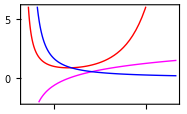

```mathematica
Plot[{Gamma[x+1],PolyGamma[x+1],PolyGamma[1,x+1]},{x,-1,4},
          PlotRange->{-2,6},PlotStyle->{Red,Magenta,Blue},
          PlotLegends->"Expressions",Frame->True]
```

证明：lim_(z→-n) (ψ(z))/(Γ(z))=-(-1)^nn!    其中 n 为正整数

```mathematica
Limit[PolyGamma[z]/Gamma[z],z->-n,Assumptions->{n>0,n∈Integers}]
```

-(-1)^n n!

由 digamma函数的定义易证：ψ(z+1)≡(Γ'(z+1))/(Γ(z+1))=1/z+(Γ'(z))/(Γ(z))=1/z+ψ(z)    递推关系

从而：ψ(z)=ψ(z+n+1)-1/z-1/(z+1)-⋯-1/(z+n-1)-1/(z+n),

这里因为 z→-n，故把 ψ(z)写成上式，以保证 ψ(z+n+1) 在 z→-n 时趋于 ψ(1) 是解析的。

类似于 Γ(z)，ψ(z) 在 Re z>0 解析，在 z 为 0 或负整数时是单极点，但留数为 -1，与 Γ(z)不同。

```mathematica
Residue[Gamma[z],{z,-n},Assumptions-> {n≥ 0,n∈Integers}]
Residue[PolyGamma[z],{z,-n},Assumptions-> {n≥ 0,n∈Integers}]
```

(-1)^-n/(n!)

-1

另一方面：Γ(z)=(Γ(z+n+1))/(z(z+1)(z+2)⋯(z+n)),  这里也因为 z→-n 而把 Γ(z)表为：Γ(z+n+1)

从而

lim_(z→-n) (ψ(z))/(Γ(z))=lim_(z→-n) (ψ(z+n+1)-1/z-1/(z+1)-⋯-1/(z+n))/((Γ(z+n+1))/(z(z+1)(z+2)⋯(z+n)))
=lim_(z→-n) (z(z+1)⋯(z+n-1)[(z+n)ψ(z+n+1)-(z+n)/z-(z+n)/(z+1)-⋯-1])/(Γ(z+n+1))
,  其中：ψ(z) 在 Re z>0 解析 
=(-n)(-n+1)⋯(-1)=-(-1)^nn!

另证：以上证明利用了迭代关系：ψ(z+1)=1/z+ψ(z)，从而

ψ(z)=ψ(z+n+1)-1/z-1/(z+1)-⋯-1/(z+n-1)-1/(z+n)

可能不大习惯。以下利用 Laurent 展开加以证明。

由 Γ(z)=(Γ(z+n+1))/(z(z+1)(z+2)⋯(z+n))，知：z=-n 是单极点 且 Res Γ(-n)=(-1)^n/(n!)

而由定义： ψ(z)=(Γ'(z))/(Γ(z))  及第三章最后的例题知：z=-n 是单极点且 Res ψ(-n)=-1

从而：Γ(z)=(Res Γ(-n))/(z+n)+a_0+a_1(z+n)+…

ψ(z)=(Res ψ(-n))/(z+n)+b_0+b_1(z+n)+…

(ψ(z))/(Γ(z))=(Res ψ(-n)+b_0(z+n)+(b_1(z+n))^2+…)/(Res Γ(-n)+a_0(z+n)+(a_1(z+n))^2+…)

上式两边同取极限：lim_(z→-n) (ψ(z))/(Γ(z))=(Res ψ(-n))/(Res Γ(-n))=-(-1)^nn!

思考：已知 ψ(1)=-γ ，试导出 Γ(z) 的Weierstrass 乘积表示：1/(Γ(z))=z ⅇ^(γ z)(∏_(k=1))^∞(1+z/k)ⅇ^(-z/k)

参见：亚纯函数的极点展开和整函数的乘积展开一节

### Beta 函数

Beta 函数是由第一类 Euler 积分定义的二元复变函数：

B(p,q)=∫_0^1 (t^(p-1)(1-t))^(q-1)ⅆt,      Re p>0, Re q>0

令 t=sin^2 θ，可得

B(p,q)=2∫_0^(π/2) sin^(2p-1)θ cos^(2q-1)θⅆθ,      Re p>0, Re q>0

与 Gamma 函数的关系

Γ(p)=∫_0^∞ ⅇ^-t t^(p-1)ⅆt→^(令：t=y^2)=2∫_0^∞ ⅇ^(-y^2)y^(2p-1)ⅆx,  同理：Γ(q)=2∫_0^∞ ⅇ^(-x^2)x^(2q-1)ⅆy

Γ(p)Γ(q)=4∫_0^∞ ∫_0^∞ ⅇ^(-y^2)y^(2p-1)ⅇ^(-x^2)x^(2p-1)ⅆxⅆy,  化为极坐标：x=r cos θ,  y=r sin θ
=4∫_(r=0)^∞ ∫_(θ=0)^(π/2) (ⅇ^(-r^2)(r sin θ))^(2p-1)(r cos θ)^(2q-1)rⅆrⅆθ
=4∫_(r=0)^∞ ⅇ^(-r^2)r^(2p+2q-1)ⅆr∫_(θ=0)^(π/2) sin^(2p-1)θ cos^(2q-1)θⅆθ,     令：t=r^2
=Γ(p+q)B(p,q)

B(p,q)=(Γ(p)Γ(q))/(Γ(p+q))

以上证明在 Re p>0, Re q>0 条件下进行，但上式右边可解析延拓至整个复平面，

故 Beta 函数可解析延拓至整个 p 平面和 q 平面。

理解：例如函数 w=√z=r^(1/2)ⅇ^(ⅈ θ_z/2)，θ_z=arg z
做割线为从原点沿正实轴到无穷远
在 z≠0的任意一点 A，
无论怎么折腾，只要不穿过割线
趋于 A 点时，辐角 θ_z=arg z 没有变
函数值 w 的辐角 θ_w=arg w 也 不变。
但对于原点（是枝点），
沿上岸接近原点与绕到下岸接近原点
（如图黄、蓝线） θ_z=arg z 分别是 0 和 2 π
函数值的辐角 θ_w=θ_z/2 分别为：0与 π         -Graphics-

不同的辐角 θ_w 对函数值本身可能没有影响（模趋于 0），但对函数的变化率可能产生影响

也即：以不同方式→0，变化率的极限值可能不同。因而枝点被认为导数不存在，是奇点。